```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
(* trigger autoload Failure formatting *)
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

## update

```mathematica
PacletUninstall["Lint"]
```

```mathematica
PacletInstall["/Users/brenton/development/stash/COD/lint/build/paclet/Lint-999.paclet"]
```

PacletObject[Lint,999,<>]

```mathematica
PacletDirectoryAdd["/Users/brenton/development/stash/COD/lint/Lint"];
```

```mathematica
FindFile["Lint`"]
```

/Users/brenton/development/stash/COD/lint/Lint/Kernel/Lint.wl

```mathematica
PacletUpdate["Lint","UpdateSites"->True]
```

PacletObject[Lint,0.15,<>]

## Init

```mathematica
$MessagePrePrint=.
```

```mathematica
Off[General::stop]
```

The AST package must be built first. Change these paths to point to your location of ASTTools.

```mathematica
Needs["Lint`"]
Needs["Lint`ImplicitTimes`"]
```

```mathematica
installation=$InstallationDirectory<>"/";
```

```mathematica
protos="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/";
```

```mathematica
stash="/Users/brenton/development/stash/";
```

```mathematica
cvs="/Users/brenton/development/cvs-development/";
```

```mathematica
github="/Users/brenton/development/github-development/";
```

```mathematica
other="/Users/brenton/development/other-development/";
```

```mathematica
examples="/Users/brenton/Downloads/WLCodeExamples/";
```

```mathematica
(*lineHashExclusions=<|
(*kernelMain / protos*)
"Kernel/StartUp/Algebra/NumberField.m"->{"03d1240b54171896"},
"Kernel/StartUp/Control/CodeGeneration.m"->{"19412d627d6b7e46","694323f420e68a25"},
"Kernel/StartUp/Convert/NBMLConvert.m"->{"31f2e8ea294f80bd"},
"Kernel/StartUp/DataPaclets/PsychrometricPropertyData.m"->{"6999fce83dac548b","62238af94392477c","5f23d2758de3a21f",
"40f8d6c9b6d4b08a"},
"Kernel/StartUp/DateTime/CalendarAstronomy.m"->{"31a45a1c1b35fda4","173ed72efc7557a7"},
"Kernel/StartUp/DSolve/DSolveIntegroDifferentialEquation.m"->{"70806c5ac6cccbc6"},
"Kernel/StartUp/Explore/Explore.m"->{"204f684487679053"},
"Kernel/StartUp/Explore/PlotExplorer.m"->{"04983530c6c11391"},
"Kernel/StartUp/FunctionInterpolation.m"->{"4599dd69670d0292"},
"Kernel/StartUp/GIS/GeoModel.m"->{"1c27000519cde9ed","10c8a44b236ba029","62d9fd8900ee8261"},
"Kernel/StartUp/GIS/GeoProjections.m"->{"7a14bc508f22709f","16911bb751b91ee7","4ab33b1dd799a83b","0637c66fd64e707e","4ab33b1dd799a83b",
"7b1ba946278cbf17","069bf6e928e916b2","3ad653f01f4d5f33","27b3a9c0108ed1d9","466dc1ee9093b6db","6635fbe2602a13ba"},
"Kernel/StartUp/Graphics/GraphicsFormat.m"->{"3f105940ae99f908","5024bd6c9eeaa56a","073b391afdc9e837","6440cadea419ea41","2c1db2175672be73"},
"Kernel/StartUp/ImageProcessing/CompositionOps/Compose.m"->{"3fb6e2e0b3ea6a14"},
"Kernel/StartUp/ImageProcessing/Matrices/Common.m"->{"76146a30598981ea","7b13c36587c903e0","6efd63b1fabadf50","78abe098d3fa2871"},
"Kernel/StartUp/Integrate/trig.m"->{"312f6a2a05f7a632"},
"Kernel/StartUp/LinearAlgebra/TransformConstructors.m"->{"014b2c47dae470d2","014b2c47dae470d2","72725bb3496e1116"},
"Kernel/StartUp/Manipulate.m"->{"63c6508d29a231dc","63c6508d29a231dc","21ebb11eb5eb8ff3","3b6779e059e8cafc",
"0c7d9bf871d837b7","50f1486f6187d938","2e8fd78da03300b3","3f745ba41220d3a6","7f9855eae09a71b5","7bd2fd3eff54b2d4","7ffa231626579ddd"},
"Kernel/StartUp/NDSolve/EquationProcessing/DiscontinuityValues.m"->{"5fb198b362503f4b","26468f9b95a56282"},
"Kernel/StartUp/NDSolve/FEM/FEMBoundaryConditions.m"->{"6708e1f79d36c5d2"},
"Kernel/StartUp/NDSolve/FEM/FEMDiscretization.m"->{"63df233ff906cdba","2de223d7462bc969","5377d7bb94813731","31d1946443afe858","39bbde8a59d1cfa1"},
"Kernel/StartUp/NDSolve/FEM/FEMMesh.m"->{"77b81b15ce83c44f","0f0a5515359f1ba1","01d8b85bc47897c6","4ae6660d412a6cf4","7ca7dbcc62b27784"},
"Kernel/StartUp/NDSolve/FEM/PDEParser.m"->{"61d265e8b87ca6f4","6928ae8049c0eb94"},
"Kernel/StartUp/Network/GraphBoxes.m"->{"44471c9adf36998f","41d6756484bc28c1","41d6756484bc28c1"},
"Kernel/StartUp/Network/GraphChart.m"->{"52ad6f2cf8fc9508"},
"Kernel/StartUp/NIntegrate/SimplexQuadrature.m"->{"2a1e92e5bdb9b59f"},
"Kernel/StartUp/Optimization/NMinimize.m"->{"31f2e8ea294f80bd","33c0e18754f1ca87","05fbc58560d62489"},
"Kernel/StartUp/Reduce/Optimization.m"->{"7354fe94335abd0e"},
"Kernel/StartUp/Reduce/Thue.m"->{"273f4daef0b9ac4e"},
"Kernel/StartUp/Reduce/TRoots.m"->{"6bf17ab528ab3634","0ae2ab78930a6b4b"},
"Kernel/StartUp/Regions/Meshes/MeshGraphicsBox.m"->{"15012f9b6e615e3a","4b582a793c7c4e50"},
"Kernel/StartUp/Regions/Meshes/MeshUtilities.m"->{"7f306bf072dd37b5"},
"Kernel/StartUp/Regions/RegionFunctions/RandomPoint.m"->{"4616b599f2fa37d6"},
"Kernel/StartUp/Regions/RegionGraphics/RegionGraphicsBox.m"->{"338667ce2d251209"},
"Kernel/StartUp/Regions/RegionOperations/SRRelations.m"->{"1c8c83222f5d0c82"},
"Kernel/StartUp/Regions/RegionTransforms/AffineTransforms.m"->{"2fc60f01bef7a902","4222fdf69a8baeb0","6d2e16e85a7da416",
"2ea17edaba8aba31"},
"Kernel/StartUp/Regions/RegionUtilities/SpecialRegions.m"->{"33c67ab17bccac81","6f7b9138db2656ae"},
"Kernel/StartUp/RSolve/RecurrenceTable.m"->{"014747e395d6518b"},
"Kernel/StartUp/Sound/AudioCapture.m"->{"70b00628974564e6"},
"Kernel/StartUp/Sound/AudioUtilities.m"->{"0c6bdb7c4ab10f36"},
"Kernel/StartUp/SpatialAnalysis/PointProcesses/PointProcesses.m"->{"40c32a0afe9384af","550af0dedee0afb9","22e6927b43e01027",
"284d0d33f595fcdb","6bd16240c77f9482","03c86d49bde23991","7ca7fd92e93d67f5"},
"Kernel/StartUp/SpecialFunctions/Spheroidal.m"->{"6e16f82800922386","7906253e39b74fd7","08b3b641ba36d555","03167346aea55881",
"76bc31f32ce72935","185c0324aee7fad0","2985a2a42076c0d3","17f8da2ff386525e","7a2d0f7e605f7eef","7497735755f9e9cf","2e3ff306dc7be3cd",
"0bad421509a91f64","2e3ff306dc7be3cd","0bad421509a91f64","78a49a1be39f66ac","2b53ad8ed694d4af","78a49a1be39f66ac","02fde28cdc8f8515",
"02fde28cdc8f8515"},
"Kernel/StartUp/Statistics/ContinuousDistributions/MultinormalDistributions.m"->{"18b70af3b9aa0f27","1023469f6ea06c4a"},
"Kernel/StartUp/Statistics/NonparametricDistributions/HistogramDistribution.m"->{"0fe8fdcd7760d2cb"},
"Kernel/StartUp/Statistics/Solvers/RandomVariate.m"->{"49ab5df2e8ce36ff"},
"Kernel/StartUp/Sum/SumFiniteSpecialRules.m"->{"08dc11ca3cd2fc44","4109b1ef6072f1b5","16132a05552dd3b0","0e1b0aefcfe083c9",
"4d1cc96fc29f93ef","120217d1ac98d252","51c61a396b951c18","050c056a38b6efa2","77da786bdf4b07e7","2388c63276ff1ed8","480b9699e7ec777d",
"0c74efa034f34341","469e6b373339a737","3c9814cf6756ca4a","30db291a9cf2752e"},
"Kernel/StartUp/Sum/SumInfiniteSpecialRules.m"->{"009b8100f4b38d4e","33eec2bfb4fb29be","1c66ca31096b4421","340a70642d837be3",
"1cd1f097208aa8be","1d30b8df4ebb5fc5","3261b5e0bf425424","1668474f3ea06acf","18c21cb746c4956d","01672fe76d75bb57","55e55046d08fb2d9",
"463ff09673a32ef5","5384051f170c90d3","65927912de0c6a4b","1ebf64bb9169f0bf","5b475f05ba1dceb3","3f5cfe0face42598","0dc05741a3d477b5",
"720a18b2fcabb4d3","1e79bc820b2afb07","64bd987050fc090d","5f9b01f249e3fec3","01e966b9ca6dbeca","5bbd805809ab8919","55fa242385113005",
"112c28588b8ebbd5","14b570c669f658c2","7720cbbc036ce346","35e674e891a87962","7e4130936ee98e84","37b3067ce5d305f6","5e74cc8f396822d0",
"309087f00a929548","0f5235e753aa120f","379f64387817033d","36f8a1a0bad13b2f","18884cbd72648cbb","6518ec105bcd8293","73b8a2d10a0b779a",
"393c0afbfddd8109","5bec2a3708ed6cf8","544eca99045d98c0","35d50fa3cc60d710","0af15edc3a2ea149","2a2c4348641806bc","6d1f39199d250a45",
"29c090d03c69b7d8","0430419de17637a3","1f78eca9ca7a4729","2e552ed214f34275","5d882a9a6b0ac211","3419bf4dc8f7dfec","6b0844d984ad016a",
"0921cd365e323fde"},
"Kernel/StartUp/SymbolicTensors/SymbolicTensors.m"->{"05fec030e95e6476","3eb8e9739ab3e438"},
"Kernel/StartUp/Typeset/Dynamic.m"->{"57f673e76ea2cc7c","72b37c39f1696743","289982d63417f317"},
"Kernel/StartUp/Typeset/TypesetInit.m"->{"11e7d903a5843287","7373773d50cfdf2a"},
"Kernel/StartUp/Typeset/SpokenString.m"->{"33a602646fbb3c07"},
"Kernel/StartUp/Visualization/BarChart3D.m"->{"3203e7bd35a5e4f0","3203e7bd35a5e4f0","7dcd17b4dc392932"},
"Kernel/StartUp/Visualization/Gauges.m"->{"39f354a522826d6a","30fbab6141beb9a6","4482be4096d686e0","72fcd59133313277",
"59ac5f4b7d8f64c8","324903fb58803084","500eed1e82e8688b","02031082ce4514d7"},
"Kernel/StartUp/Wavelets/BattleLemarieWavelet.m"->{"49037cf904a93e45","3b8fe5be4be833ef"},
"Kernel/StartUp/Wavelets/LiftingFilter.m"->{"38731099c22fe90d"},
"Messages/errmsg.m"->{"70e96836925e4183","68022076f22e34f1","0ca5c2437e5f1330","1ed9c6e1816179a3","414b1647a49bb7fd","026120075106fd13",
"0b886d39b01873a7"},

(* installation *)
"AddOns/Applications/CompiledFunctionTools/CompiledFunctionTools.m"->{"0da7a7d28cfca989"},
"AddOns/Applications/CompiledFunctionTools/PrintCode.m"->{"2ee70999758761e4"},
"AddOns/ExtraPackages/DifferentialEquations/NDSolveProblems.m"->{},
"AddOns/Packages/Combinatorica/Combinatorica.m"->{"4c77ed39f6de1bbf"},
"AddOns/Packages/FiniteFields/FiniteFields.m"->{"2b861e17c93dc12a","017a494002e954e2"},
"AddOns/Packages/FourierSeries/FourierSeries.m"->{},
"AddOns/Packages/LinearRegression/LinearRegression.m"->{"2a72cde271a6182f"},
"AddOns/Packages/MultivariateStatistics/MultiDescriptiveStatistics.m"->{"18fdc749f03c0145"},
"AddOns/Packages/NonlinearRegression/NonlinearRegression.m"->{"781b523611463a94"},
"AddOns/Packages/Splines/Splines.m"->{"3bbaf0e5bd799e3c"},
"AddOns/Packages/VariationalMethods/VariationalMethods.m"->{"639685c94ca4306e"},
"SystemFiles/Components/CCodeGenerator/CCodeGenerator.m"->{"78497442d3f98d1b"},
"SystemFiles/Components/Compile/AST/Macro/Builtin/Conditional.m"->{"1d73c3819ade1768","1e0ad42179349164","0db845947764e204",
"0bf9ba4da619f4a3"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Break.m"->{"64499f2d5c2d329e"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Continue.m"->{"335607c5839b8cbf"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Return.m"->{"3b9c3fb7da3d5426"},
"SystemFiles/Components/Compile/Utilities/Language/SymbolAreasTable.m"->{"55eac21c2ba1bb7f","2d3d344d0445c106",
"42f97ad40a0821d4"},
"SystemFiles/Components/CompileUtilities/RuntimeChecks/RuntimeChecks.m"->{"0f40561fc4b61bbe","2dfea9ca8b7e9ec2",
"54d7b7b60d50741a","10c16e404e4c7412","165bc22739e6fa11","0f831b782569644e"},
"SystemFiles/Components/FunctionResource/Kernel/Utilities.m"->{"2cc0df58b7106f2e"},
"SystemFiles/Components/NeuralNetworks/MXNet/ToPlan.m"->{"225c6ca998056014","13c44f36e1a68511"},
"SystemFiles/Components/NeuralNetworks/NetTrain.m/JIT.m"->{"5087244a89f175d7","72558357da1e3c14","2528f9b225dac1f6",
"409452941c481b4b"},
"SystemFiles/Components/NeuralNetworks/Types/Coerce.m"->{"6cbcc1bacc9abad0","5da750900e4b0c93","3444c9323cc3f1a9",
"0271ba3207bba61f","0922816608f8da27"},
"SystemFiles/Components/NeuralNetworks/Types/Predicates.m"->{"5f3ef3955f71dcbe","369d54e3e40141b4","28e9cba7b120d9ae",
"734829e822cd569a","365bcb383e4d8bdb","54f3578146c96f37","528b2f425df6d9cd","557d176b6b2360b8","6c11c4c9de755117",
"3ed9c254b70e14b3","05fca00977088c72","24424346dc2c3c83","457dead36e959162","1d60aacf12acbdd4","7c63017a335427ca",
"75fd81bd944a22f4","09987fecf69372cc","09b638849bfd73e4","1f3386e1cb7ea1c6","284459d5c9d47a80",
"375689a102c07934","457ef592ca9338cd","177a4e532d1ecee9","071f231c47fd18be","2e2a03e35a605425","2f67aa096ed90221"},
"SystemFiles/Components/NeuralNetworks/Types/Properties.m"->{"28587a95a919c11c","4675793b836de53e","734829e822cd569a",
"31dc3cb00a1358ac","40275c504d7191c5","5087244a89f175d7","4c8634f4d0b61ad8","10f37f55b34429ba","54bdcb4da83c16dd",
"549d1d5e6fbffbca"},
"SystemFiles/Components/NeuralNetworks/Types/Random.m"->{"3f0b54e666328d26","0bc6b7514e62c98c","2373704cfd1fd33a",
"75a1121337c1ad03","0669da00893fbb21","492dfb7c60ce1f5c","3afa900664d8a6f3","4fb38cbd35da0cdf","53b84e89c22b77a7",
"6e882b56777d5e5b","063b8c620220f928","6d3174c97f5c9ee6","74cd0f4217fd7b71","4ed3a9d412f4ec6f","1a6c7be4442d85ff"},
"SystemFiles/Components/NeuralNetworks/Types/TypeForm.m"->{"63ba7b4cb5c1faf8","5af263d8a51abaa9","2a6a2b31c958546b",
"7f60794836b6c443","29feed4f7a833f29","59409e0c21b05eb6","393100f1101d9ffb","7e98869700297526","74cd0f4217fd7b71",
"4190e3d36d0835f3","6ff610a5ba1a66da","0641cbba44f4ca04","3a17989bc0e27dd6"},
"SystemFiles/Components/NeuralNetworks/Types/Types.m"->{"75d05b7eafb55daa","55ff8aa2423d5468","5d4fd4861152a641",
"17448ddada285ac6","343c0b3929312df2"},
"SystemFiles/Components/WebAudioSearch/Kernel/WebAudioSearch.m"->{"5dc72403f4780fa1","085f5cdd394e3d7c","2ad8f93badfad71a"},
"SystemFiles/Devices/DeviceDrivers/Serial.m"->{"57ff70ba95d4c2ec"},
"SystemFiles/Kernel/TextResources/English/Messages.m"->{"70e96836925e4183","68022076f22e34f1","1ed9c6e1816179a3",
"0b886d39b01873a7","0ca5c2437e5f1330","414b1647a49bb7fd","026120075106fd13"},
"SystemFiles/Links/Databases/Databases/Common/Common.m"->{"0399a740b3cde7f1","7e16465b0f01aedf"},
"SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionCompiler.m"->{"73e4b3175535ddf4"},
"SystemFiles/Links/GPUTools/CompileCodeGenerator.m"->{"78497442d3f98d1b"},
"SystemFiles/Links/GPUTools/SymbolicGPU.m"->{"5bc5be7e7db96d42","79ae15d998ad6b9e","6e28d7b590e2b94a","42cba421cd99c297","569eb9731485259d"},
"SystemFiles/Links/GPUTools/WGLPrivate.m"->{"1b3e9c9e332d4f98","0f2dbae3e06207b8","177367bae68f5d49","79581a5b6f95c7da","497e31b051e5e3dd",
"50a5caab2dcab938","2c35e17facaa7fa3","255873cd4cd2cfaa","47fb215e76336e6e","47fb215e76336e6e","114fa7b54fce134f","5081c6edc7560ead",
"03926f8b9ed14b88","104e7ab00261eb67"},
"SystemFiles/Links/IPOPTLink/IPOPTLink.m"->{"37614a48c96c3933","36c30c2a6a2818d6","36c30c2a6a2818d6","36c30c2a6a2818d6","4eadd2d17535cb38"},
"SystemFiles/Links/SecureShellLink/Kernel/Remote.wl"->{"326714fee09a9ac7","326714fee09a9ac7"},
"SystemFiles/Links/SerialLink/SerialLink.m"->{"6fce25b343c1b272","240e812787f09206"},
"SystemFiles/Links/WebServices/Kernel/Implementation.m"->{"3559460bc280923e"},

(*repos*)
"Compile/Compile/AST/Macro/Builtin/Conditional.m"->{"1d73c3819ade1768","1e0ad42179349164","0db845947764e204",
"0bf9ba4da619f4a3"},
"Compile/Compile/Core/CodeGeneration/Backend/CXX/CXX.m"->{"66b82c229e584d85","58744f56b79779e9"},
"Compile/Compile/Core/IR/Lower/Primitives/Break.m"->{"64499f2d5c2d329e"},
"Compile/Compile/Core/IR/Lower/Primitives/Continue.m"->{"335607c5839b8cbf"},
"Compile/Compile/Core/IR/Lower/Primitives/Return.m"->{"3b9c3fb7da3d5426"},
"Compile/Compile/Utilities/Language/SymbolAreasTable.m"->{"55eac21c2ba1bb7f","2d3d344d0445c106",
"42f97ad40a0821d4"},
"CompileUtilities/CompileUtilities/RuntimeChecks/RuntimeChecks.m"->{"0f40561fc4b61bbe","2dfea9ca8b7e9ec2",
"54d7b7b60d50741a","10c16e404e4c7412","165bc22739e6fa11","0f831b782569644e"},
"CUDACompileTools/CUDACompileTools/Transforms/InstantiateMap.m"->{"30b602d59b8145a6","4ded2efc42f62f63","1b2faae3520c3558"},
"DeviceDrivers/Serial.m"->{"57ff70ba95d4c2ec"},
"GeneralUtilities/GeneralUtilities/Control.m"->{"403ab287349342f8","171897441bde5358","7afc74af8d8d568f"},
"GeneralUtilities/GeneralUtilities/EvaluationInformation.m"->{"0510938e465f7299","3138797ad33251d6"},
"GeneralUtilities/GeneralUtilities/Formatting.m"->{"05ffd75ea43a770c","5a53261bf894faa7"},
"GeneralUtilities/GeneralUtilities/Stack.m"->{"3f57b710dd40818c","75dfa25a918b48ff","14c8217dc87084cb"},
"GeneralUtilities/Tests/TextString.m"->{},
"NeuralNetworks/NeuralNetworks/MXNet/ToPlan.m"->{"225c6ca998056014","13c44f36e1a68511"},
"NeuralNetworks/NeuralNetworks/NetTrain.m/JIT.m"->{"5087244a89f175d7","72558357da1e3c14","2528f9b225dac1f6",
"409452941c481b4b"},
"NeuralNetworks/NeuralNetworks/Types/Coerce.m"->{"6cbcc1bacc9abad0","5da750900e4b0c93","3444c9323cc3f1a9",
"0271ba3207bba61f","0922816608f8da27"},
"NeuralNetworks/NeuralNetworks/Types/Predicates.m"->{"5f3ef3955f71dcbe","369d54e3e40141b4","28e9cba7b120d9ae",
"734829e822cd569a","365bcb383e4d8bdb","54f3578146c96f37","528b2f425df6d9cd","557d176b6b2360b8","6c11c4c9de755117",
"3ed9c254b70e14b3","05fca00977088c72","24424346dc2c3c83","457dead36e959162","1d60aacf12acbdd4","7c63017a335427ca",
"75fd81bd944a22f4","09987fecf69372cc","09b638849bfd73e4","1f3386e1cb7ea1c6","284459d5c9d47a80","375689a102c07934",
"457ef592ca9338cd","177a4e532d1ecee9","071f231c47fd18be","2e2a03e35a605425","2f67aa096ed90221"},
"NeuralNetworks/NeuralNetworks/Types/Properties.m"->{"28587a95a919c11c","4675793b836de53e","734829e822cd569a",
"31dc3cb00a1358ac","40275c504d7191c5","5087244a89f175d7","4c8634f4d0b61ad8","10f37f55b34429ba","54bdcb4da83c16dd",
"549d1d5e6fbffbca"},
"NeuralNetworks/NeuralNetworks/Types/Random.m"->{"3f0b54e666328d26","0bc6b7514e62c98c","2373704cfd1fd33a",
"75a1121337c1ad03","0669da00893fbb21","492dfb7c60ce1f5c","3afa900664d8a6f3","4fb38cbd35da0cdf","53b84e89c22b77a7",
"6e882b56777d5e5b","063b8c620220f928","6d3174c97f5c9ee6","74cd0f4217fd7b71","4ed3a9d412f4ec6f","1a6c7be4442d85ff"},
"NeuralNetworks/NeuralNetworks/Types/TypeForm.m"->{"63ba7b4cb5c1faf8","5af263d8a51abaa9","2a6a2b31c958546b",
"7f60794836b6c443","29feed4f7a833f29","59409e0c21b05eb6","393100f1101d9ffb","74cd0f4217fd7b71",
"4190e3d36d0835f3","6ff610a5ba1a66da","0641cbba44f4ca04","3a17989bc0e27dd6"},
"NeuralNetworks/NeuralNetworks/Types/Types.m"->{"75d05b7eafb55daa","55ff8aa2423d5468","5d4fd4861152a641",
"17448ddada285ac6","343c0b3929312df2"},
"SerialLink/SerialLink/SerialLink.m"->{"6fce25b343c1b272","240e812787f09206"},
"Streaming/Streaming/LazyList/Integration/Packing.m"->{"56cc8189d68e68ce"},
"Streaming/Streaming/Objects/References.m"->{},
"SymbolicMachineLearning/SymbolicMachineLearning/FindFormula/InputArgumentTestFindFormula.m"->{"326714fee09a9ac7",
"31f2e8ea294f80bd","31f2e8ea294f80bd"},
"TypeSystem/TypeSystem/NestedGrid.m"->{"1102829ba555ef0a","337b45658482a540","0126e31743571250","393bc3533d05232d",
"30b52c8e18d84a23","666063adb2147530","5e73236c6f38e2cf","6755030528f12566","73fac8b08b377dfb","0df2019fb2590c36",
"6dd88bf17d80e3ee","276bfb2de7885320","4c57b7c19b76e48f","3a2e18d090a02ff1"},

(*alpha*)
"alphasource/CalculateData/EntityPropertyTable/PhysicalSystemEntity.m"->{"01d6cc28b483714d"},
"alphasource/CalculateIncludes/MathematicalFunctionData/JacobiSymbol.m"->{"260c01c2d6762f58","260c01c2d6762f58","260c01c2d6762f58"},
"alphasource/CalculateParse/GeneralLibrary.m"->{"0d47950b4e1821ab","527d746237686bb9","0b87e244f6360e62","763fd034266517a0"},
"alphasource/CalculateParse/Grammar.m"->{"2b417b85f5b60ab2"},
"alphasource/CalculateParse/TemplateParser4.m"->{"18681de613ddaa16","18681de613ddaa16"},
"alphasource/CalculateScan/ChemicalThermodynamicsScanner.m"->{"2e18556759526e9b"},
"alphasource/CalculateScan/CommonSymbols.m"->{"499ddc8c7d0b96bd","37fb5f08252843d9"},
"alphasource/CalculateScan/Data/GeometryData.m"->{"647513426795059d"},
"alphasource/CalculateScan/FormulaScanner.m"->{"1087fe6f2d24fc16"},
"alphasource/CalculateScan/FunctionalDifferentiationScanner.m"->{"10b697e57d47f040"},
"alphasource/CalculateScan/IteratedObjectsScanner.m"->{"64a1c03013d80191"},
"alphasource/CalculateScan/Packages/Blackbody.m"->{"2e71c84d83bba554"},
"alphasource/CalculateScan/Packages/PlanetaryAstronomy.m"->{},
"alphasource/CalculateScan/ReduceScanner.m"->{"21a376552811e786"},
"alphasource/CalculateScan/StepByStepMath/StepByStepSimplify.m"->{"11a42d4b25a779d2"},
"alphasource/CalculateScan/UnitScannerUnitBases.m"->{"7cdb043b4313f51e"},
"alphasource/CalculateUtilities/DebuggingUtilities.m"->{"53d006cde1d33b88","5913001b08e13dd3"},
"alphasource/CalculateUtilities/DynamicUtilities.m"->{"476898ebd553cc9d"},
"alphasource/CalculateUtilities/FormatUtilities.m"->{"7aca62cf0b05ee19"},
"alphasource/CalculateUtilities/GraphicsUtilities.m"->{"3730df81df2fb4ba","0cb057b476cc324c","038baa7ed2e1895a"},
"alphasource/CalculateUtilities/ImportExport/DataRecognizer.m"->{"666cb9aed60a281a"},
"alphasource/CalculateUtilities/InfrastructureUtilities.m"->{"18b48f4c587e4066","4eb6c88c40274c9c","09720b08c7de115c","2a4aac919205d1d2"},
"alphasource/DataScience/Utils/Language.m"->{"2a8037a4e5b83548","70e3108512e77cd0","13d0c8505832d475","106e59ae5c99765c",
"0d68498b891ea465","626af03fdbf64559"},

(*other*)
"systemmodeler/WL/WSMLink/Diagram/Diagram.m"->{"4a1e9c375885b904"},


Nothing
|>;*)
lineHashExclusions=<||>;
performanceGoal="Quality";
concreteRules=Lint`ConcreteRules`$DefaultConcreteRules;
aggregateRules=Lint`AggregateRules`$DefaultAggregateRules;
abstractRules=Lint`AbstractRules`$DefaultAbstractRules;
```

```mathematica
$AdditionalRules=<||>;
```

```mathematica
Options[lintTest]={"FileNamePrefixPattern"->""};
```

```mathematica
lintTest[fileIn_String,i_Integer,OptionsPattern[]]:=
Catch[
Module[{lints,data,file,prefix,f,byteCount},
file=fileIn;

byteCount=FileByteCount[file];

If[byteCount<Lint`Private`$fileByteCountMinLimit,
Throw[ok]
];
If[Lint`Private`$fileByteCountMaxLimit<byteCount,
Throw[ok]
];

prefix=OptionValue["FileNamePrefixPattern"];

data=LintFileReport[File[file],
"LineHashExclusions"->Lookup[lineHashExclusions,StringReplace[file,StartOfString~~prefix->""],{}],
"SeverityExclusions":>severityExclusions,
"TagExclusions":>tagExclusions,
PerformanceGoal:>performanceGoal,
"ConcreteRules":>concreteRules,
"AggregateRules":>aggregateRules,
"AbstractRules":>abstractRules,
Sequence[]];

If[data[[2]]≠{},
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[data]
];
]
]
```

```mathematica
Options[implicitTimesTest]={"FileNamePrefixPattern"->""};
```

```mathematica
implicitTimesTest[file_,i_,OptionsPattern[]]:=
Catch[
Module[{data,prefix,lints},

prefix=OptionValue["FileNamePrefixPattern"];

lints=ImplicitTimesFile[File[file],PerformanceGoal->"Speed"];

If[FailureQ[lints],
Switch[lints[[1]],
"FileTooLarge"|"FileTooSmall",
Throw[ok]
,
"NotAFile"|"EncodedFile",
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[Row[{"index: ",i," ",lints[[1]],"; skipping"}]];
,
_,
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[Row[{"index: ",i," ",lints}]];
];
Throw[lints]
];

If[lints=={},
Throw[Null]
];

data=ImplicitTimesFileReport[file,lints];
If[data[[2]]≠{},
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[data]
];
]
]
```

## Lint all files

Report various issues with .m code in the product layout.

```mathematica
prefix:=stash<>"PAC/";
prefix:=stash<>"KERN/Kernel/";
prefix:=other<>"WLCodeExamples/";
prefix:=cvs<>"Mathematica/Packages/Combinatorica/";
prefix:=protos<>"Kernel/StartUp/";
prefix:=stash<>"KERN/Kernel/StartUp/";
prefix:=stash<>"COM/"
prefix=installation;
names1:=FileNames["*.m"|"*.wl",prefix,Infinity];
names2:=FileNames["*.nb",prefix,Infinity];
names=FileNames["*.m"|"*.wl",prefix,Infinity];

toDelete=Select[names,StringContainsQ[#,".git"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CVS"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CMake"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"build*"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"Tests"]&];
names=Complement[names,toDelete];

(* objective-c .m source files *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"wstp/ObjectiveMathLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"jlink/src/Mac/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"FrontEnd/Source/"~~__]];
names=Complement[names,toDelete];

(* miscellaneous files *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"autolibrarylink/AutoLibraryLink/Resources/wl-template.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"archive/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"compiletechdocs/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"projects/sublime/syntax_test_wolfram.wl"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"xmllink/"~~__]];
names=Complement[names,toDelete];

(* neuralnetworks is just too noisy because of wacky syntax everywhere *)
(*
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"neuralnetworks/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/NeuralNetworks/"~~__]];
names=Complement[names,toDelete];
*)

(*
Directory, not a file
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"neuralnetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];

(* encoded *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"AddOns/Applications/EntityFramework/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"AddOns/Applications/QuantityUnits/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/Interpreter/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/GeometrySearch/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/MicrocontrollerKit/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/WSMCore/WSMCore.app/Contents/Mathematica/WSMLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Links/UnityLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/ChannelFramework/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/EmbeddedSystemsTools/"~~__]];
names=Complement[names,toDelete];

(* script *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"Documentation/English/System/ExampleData/script.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"mxnetlink/MXBuild/build_mx.m"]];
names=Complement[names,toDelete];

(* files are too large *)
toDelete=Select[names,FileByteCount[#]>3.0*^6&];
names=Complement[names,toDelete];
```

5682

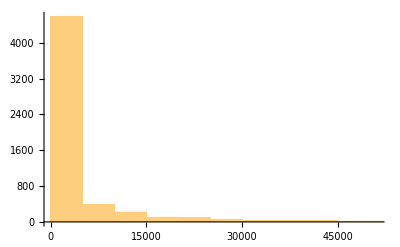

```mathematica
Length[names]
Histogram[FileByteCount/@names,{5000}]
```

```mathematica
Lint`Private`$Debug=xTrue;
Lint`Report`Private`$Debug=xTrue;
Lint`Format`Private`$Debug=xTrue;
$DebugLoop=xTrue;
$visuals=xTrue;
Lint`Format`$Interactive=xTrue;
Lint`Format`$NewLintStyle=True;
Lint`Report`$Underlight=xTrue;
```

```mathematica
severityExclusions:={"Formatting","Remark"};
severityExclusions:={"Formatting"};
severityExclusions:={"Formatting","Remark","Warning","Error"};
severityExclusions:={"Formatting","Remark"};
severityExclusions={"Formatting","Remark"};
```

```mathematica
performanceGoal="Speed";
```

```mathematica
tagExclusions:=Lint`Report`$DefaultTagExclusions~Join~{"UnusedVariables","UnusedBlockVariables",
"NotContiguous","StrayLineContinuation","UndocumentedCharacter","ObsoleteSymbol","ExperimentalSymbol"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","DuplicateClauses"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","TopLevel","Blank","ImplicitTimesStrings","DuplicateClauses","PostfixDifferentLine","UnexpectedCharacter","MissingFunction","SystemPatternBlank","DifferentLine"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","TopLevel","Blank","ImplicitTimesStrings","DuplicateClauses","PostfixDifferentLine","UnexpectedCharacter","MissingFunction","SystemPatternBlank","DifferentLine","LogicalConstant","WithArguments","UnexpectedSemicolon","ImplicitTimesBlanks","PrefixPlus","ExpectedSymbol","SuspiciousPrivateContext","SuspiciousRuleFunction","SuspiciousPatternBlankOptional","DotDifferentLine","StrangeCall"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","ModuleArgumentsEmpty","WithArgumentsEmpty","LogicalConstant","CallDifferentLine","DuplicateKeys","DuplicateClauses","InfixBinaryAtQuirk","BlockArgumentsEmpty"};
tagExclusions={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","ModuleArgumentsEmpty","WithArgumentsEmpty","LogicalConstant","CallDifferentLine","DuplicateKeys","DuplicateClauses","InfixBinaryAtQuirk","BlockArgumentsEmpty","TopLevelList","TopLevelAssociation"};
```

```mathematica
Lint`Report`Private`$ConfidenceLevel=0.0;
```

```mathematica
Lint`Private`$fileByteCountMinLimit=0.02*^6;
Lint`Private`$fileByteCountMaxLimit=4.0*^6;
```

```mathematica
Lint`External`$Editor="Sublime Text";
```

```mathematica
$ProcessID
```

62796

```mathematica
start=1;
```

```mathematica
x=start;
file=None;
Print["Linting ", Length[names[[start;;]]]," files"];
Print["Current file: ",Dynamic[Short[file]]];
Print["Current file size: ",Dynamic[FileSize[file]]];
Print["Current index: ",Dynamic[x]];
If[$visuals,
Print[Grid[{
{"concrete parse",Dynamic[AST`Library`$ConcreteParseTime],ProgressIndicator[Dynamic[AST`Library`$ConcreteParseProgress],{0,100}]},
{"aggregate parse",Dynamic[AST`Abstract`$AggregateParseTime],ProgressIndicator[Dynamic[AST`Abstract`$AggregateParseProgress],{0,100}]},
{"abstract parse",Dynamic[AST`Abstract`$AbstractParseTime],ProgressIndicator[Dynamic[AST`Abstract`$AbstractParseProgress],{0,100}]},
{"concrete lint",Dynamic[Lint`$ConcreteLintTime],ProgressIndicator[Dynamic[Lint`$ConcreteLintProgress],{0,100}]},
{"aggregate lint",Dynamic[Lint`$AggregateLintTime],ProgressIndicator[Dynamic[Lint`$AggregateLintProgress],{0,100}]},
{"abstract lint",Dynamic[Lint`$AbstractLintTime],ProgressIndicator[Dynamic[Lint`$AbstractLintProgress],{0,100}]},
{"","",Dynamic[PieChart[{AST`Library`$ConcreteParseTime,AST`Abstract`$AggregateParseTime,AST`Abstract`$AbstractParseTime,Lint`$ConcreteLintTime,Lint`$AggregateLintTime,Lint`$AbstractLintTime},ImageSize->Tiny,ChartLegends->{"concrete parse","aggregate parse","abstract parse","concrete lint","aggregate lint","abstract lint"}]]}
},Alignment->Right]];
];
Print[Row[{"overall",Spacer[10],ProgressIndicator[Dynamic[x],{0,Length[names]}]}]];
Scan[(
file=#;

Which[
TrueQ[$DebugLoop],
Print[x," ",file]
,
Mod[x,100]==0,
Print[x," ",file];
NotebookSave[EvaluationNotebook[]]
];

AST`Library`$ConcreteParseProgress=0;
AST`Abstract`$AggregateParseProgress=0;
AST`Abstract`$AbstractParseProgress=0;
Lint`$ConcreteLintProgress=0;
Lint`$AggregateLintProgress=0;
Lint`$AbstractLintProgress=0;
AST`Library`$ConcreteParseTime=Quantity[0,"Seconds"];
AST`Abstract`$AggregateParseTime=Quantity[0,"Seconds"];
AST`Abstract`$AbstractParseTime=Quantity[0,"Seconds"];
Lint`$ConcreteLintTime=Quantity[0,"Seconds"];
Lint`$AggregateLintTime=Quantity[0,"Seconds"];
Lint`$AbstractLintTime=Quantity[0,"Seconds"];
(*res=lintTest[file,x,"FileNamePrefixPattern"->prefix];*)
(*res=implicitTimesTest[file,x,"FileNamePrefixPattern"->prefix];*)
res=lintTest[file,x,"FileNamePrefixPattern"->prefix];
If[res=!=ok&&$visuals,
Pause[2.0];
];
x++;
)&
,
names[[start;;]]
]//AbsoluteTiming
```

Linting 5682 files

Current file:

Current file size:

Current index:

overall

index: 47 AddOns/Applications/CompiledFunctionTools/CompiledFunctionTools.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/CompiledFunctionTools/CompiledFunctionTools.m
 |  | 
line  21: |  |   | B | o | o | l | e | a | n | : | : | u | s | a | g | e |   | = |   | " | B | o | o | l | e | a | n |   | r | e | p | r | e | s | e | n | t | s |   | a |   | b | o | o | l | e | a | n |   | t | y | p | e |   | f | o | r |   | a |   | C | o | m | p | i | l | e | d | F | u | n | c | t | i | o | n | . | " |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 215: |  |   | F | r | o | m | T | y | p | e | E | n | u | m | [ | 1 | ] |   | = |   | B | o | o | l | e | a | n |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 224: |  |   | T | o | T | y | p | e | E | n | u | m | [ | B | o | o | l | e | a | n | ] |   | = |   | 1 |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 232: |  |   | t | o | S | h | o | r | t | N | a | m | e | [ | B | o | o | l | e | a | n | ] |   | : | = |   | " | B | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 266: |  |   | g | e | t | I | n | s | t | r | u | c | t | i | o | n | [ | l | _ | , |   | { | C | C | R | E | T | } | ] |   | : | = |   | I | n | s | t | r | u | c | t | i | o | n | [ | R | e | t | u | r | n | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Return appears but is not called.
Did you mean Return[]?11814689Delimiter
 |  | 
 |  | 
line 341: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | S | e | t | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   | r | e | g | s | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 349: |  |   |   |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | } | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 364: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | E | q | u | a | l | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 365: |  |   |   |   | M | a | p | [ | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | # | } | ] |   | & | , |   | { | r | e | g | s | } | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 368: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | E | q | u | a | l | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 375: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | C | o | m | p | a | r | i | s | o | n | H | e | a | d | [ | w | h | a | t | ] | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 379: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | C | o | m | p | a | r | i | s | o | n | H | e | a | d | [ | w | h | a | t | ] | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 389: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | C | o | m | p | a | r | i | s | o | n | H | e | a | d | [ | w | h | a | t | ] | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   | M | a | p | [ | t | o | R | e | g | i | s | t | e | r | [ | { | g | e | t | T | e | n | s | o | r | [ | # | ] | , |   | # | } | ] | & | , |   | a | r | g | s | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 394: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | L | e | s | s | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 398: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | L | e | s | s | E | q | u | a | l | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 403: |  |   |   |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 412: |  |   |   |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 432: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | S | e | t | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | o | } | ] | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 433: |  |   |   |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , |   | r | e | g | s | } | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 594: |  |   |   | I | n | s | t | r | u | c | t | i | o | n | [ | X | o | r | , |   | t | o | R | e | g | i | s | t | e | r | [ | { | B | o | o | l | e | a | n | , | r | e | g | o | } | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  |

index: 80 AddOns/Applications/DocumentationSearch/Skeletonizer.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/DocumentationSearch/Skeletonizer.m
 |  | 
line 1123: |  |   | c | o | n | v | e | r | t | T | o | S | t | r | i | n | g | [ | c |   | : |   | T | e | m | p | l | a | t | e | B | o | x | [ | _ | , |   | " | R | e | f | L | i | n | k | " | | | " | O | r | a | n | g | e | L | i | n | k | " | | | " | B | l | u | e | L | i | n | k | " | | | " | W | e | b | L | i | n | k | " | | | _ | , |   | _ | _ | _ | ] | ] |   | : | = |   | c | o | n | v | e | r | t | T | o | S | t | r | i | n | g | [ | c | [ | [ | 1 | , | 1 | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  |

index: 96 AddOns/Applications/InflationAdjust/Kernel/InflationAdjust.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/InflationAdjust/Kernel/InflationAdjust.m
 |  | 
line 265: |  |   | T | o | D | a | t | e | d | U | n | i | t | [ | u | n | i | t | _ | S | t | r | i | n | g | , |   | D | a | t | e | _ | ? | D | a | t | e | L | i | s | t | Q | ] |   | : | = |   | D | a | t | e | d | U | n | i | t | [ | u | n | i | t | , |   | D | a | t | e | ] |   | / | ; | Q | u | a | n | t | i | t | y | U | n | i | t | s | ` | P | r | i | v | a | t | e | ` | c | o | u | l | d | B | e | A | C | u | r | r | e | n | c | y | Q | [ | u | n | i | t | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 266: |  |   | T | o | D | a | t | e | d | U | n | i | t | [ | u | n | i | t | _ | S | t | r | i | n | g | , |   | D | a | t | e | _ | I | n | t | e | g | e | r | ] |   | : | = |   | D | a | t | e | d | U | n | i | t | [ | u | n | i | t | , |   | { | D | a | t | e | } | ] |   | / | ; | Q | u | a | n | t | i | t | y | U | n | i | t | s | ` | P | r | i | v | a | t | e | ` | c | o | u | l | d | B | e | A | C | u | r | r | e | n | c | y | Q | [ | u | n | i | t | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 267: |  |   | T | o | D | a | t | e | d | U | n | i | t | [ | u | n | i | t | _ | S | t | r | i | n | g | , |   | D | a | t | e | _ | ? | D | a | t | e | O | b | j | e | c | t | Q | ] |   | : | = |   | W | i | t | h | [ | { | d |   | = |   | D | a | t | e | L | i | s | t | [ | D | a | t | e | ] | } | , |   | D | a | t | e | d | U | n | i | t | [ | u | n | i | t | , | d | ] |   | / | ; | A | n | d | [ | Q | u | a | n | t | i | t | y | U | n | i | t | s | ` | P | r | i | v | a | t | e
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  |

100 /Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/LightweightGridClient/Information.m

index: 102 AddOns/Applications/LightweightGridClient/LightweightGridClient.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/LightweightGridClient/LightweightGridClient.m
 |  | 
line  603: |  |   | " | - | - | - |   |   | S | t | a | r | t | O | f | F | u | n | c | t | i | o | n | s |   | - | - | - | " | ; |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  | 
 |  | 
line 1431: |  |   | " | I | d | l | e | T | h | r | e | s | h | o | l | d |   | i | s |   | a | n |   | o | p | t | i | o | n |   | t | o |   | C | P | U | B | u | s | y | Q |   | a | n | d |   | C | P | U | I | d | l | e | Q |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 1432: |  |   | t | h | a | t |   | s | p | e | c | i | f | i | e | s |   | t | h | e |   | h | i | g | h | e | s | t |   | f | r | a | c | t | i | o | n |   | o | f |   | b | u | s | y |   | C | P | U |   | t | i | m | e |   | t | o |   | c | o | n | s | i | d | e | r |   | i | d | l | e | . | " | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  | 
 |  | 
line 1434: |  |   | " | N | u | m | b | e | r | O | f | S | a | m | p | l | e | s |   | i | s |   | a | n |   | o | p | t | i | o | n |   | t | o |   | C | P | U | B | u | s | y | Q |   | a | n | d |   | C | P | U | I | d | l | e | Q |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 1435: |  |   | t | h | a | t |   | s | p | e | c | i | f | i | e | s |   | h | o | w |   | m | a | n | y |   | s | a | m | p | l | e | s |   | t | o |   | e | x | a | m | i | n | e | . | " | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  | 
 |  | 
line 1437: |  |   | " | T | r | i | m | F | r | a | c | t | i | o | n |   | i | s |   | a | n |   | o | p | t | i | o | n |   | t | o |   | C | P | U | B | u | s | y | Q |   | a | n | d |   | C | P | U | I | d | l | e | Q |   |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 1438: |  |   | t | h | a | t |   | s | p | e | c | i | f | i | e | s |   | w | h | a | t |   | f | r | a | c | t | i | o | n |   | o | f |   | l | a | r | g | e | s | t |   | a | n | d |   | s | m | a | l | l | e | s | t |   | d | a | t | a |   | e | l | e | m | e | n | t | s |   | t | o |   | d | r | o | p |   | f | r | o | m |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 1439: |  |   | c | o | n | s | i | d | e | r | a | t | i | o | n | . | " | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  |

index: 137 AddOns/Applications/Parallel/Concurrency.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/Parallel/Concurrency.m
 |  | 
line 183: |  |   | S | e | t | A | t | t | r | i | b | u | t | e | s | [ | E | v | a | l | u | a | t | i | o | n | O | b | j | e | c | t | , |   | H | o | l | d | A | l | l | C | o | m | p | l | e | t | e | ] | ; |   | S | e | t | A | t | t | r | i | b | u | t | e | s | [ | m | a | k | e | P | i | d | , |   | { | H | o | l | d | F | i | r | s | t | , | S | e | q | u | e | n | c | e | H | o | l | d | } | ] |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  |

index: 153 AddOns/Applications/Parallel/Kernels.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/Parallel/Kernels.m
 |  | 
line  200: |  |   | N | e | e | d | s | [ | " | S | u | b | K | e | r | n | e | l | s | ` | " | ] | ; |   | N | e | e | d | s | [ | " | S | u | b | K | e | r | n | e | l | s | ` | P | r | o | t | e | c | t | e | d | ` | " | ] |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  | 
 |  | 
line 1269: |  |   | $ | K | e | r | n | e | l | I | D |   | = |   | 0 | ; |   | P | r | o | t | e | c | t | [ | $ | K | e | r | n | e | l | I | D | ] |   | ( | * |   | m | a | s | t | e | r |   | k | e | r | n | e | l |   | v | a | l | u | e | , |   | f | o | r |   | s | e | q | u | e | n | t | i | a | l |   | f | a | l | l | b | a | c | k |   | * | ) |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Definition does not contain the rest of the CompoundExpression.11180111146203218891Delimiter
 |  | 
 |  | 
line 1382: |  |   | P | r | o | t | e | c | t | [ |   | K | e | r | n | e | l | O | b | j | e | c | t |   | ] | ; |   | S | e | t | A | t | t | r | i | b | u | t | e | s | [ | K | e | r | n | e | l | O | b | j | e | c | t | , | R | e | a | d | P | r | o | t | e | c | t | e | d | ] |   | ( | * |   | t | h | i | s |   | i | s |   | t | o | o |   | g | r | o | s | s |   | t | o |   | e | x | p | o | s | e |   | * | ) |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
CompoundExpression at top-level. Consider breaking up onto separate lines.11814689Delimiter
 |  |

index: 176 AddOns/Applications/StandardOceanData/Kernel/StandardOceanData.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Applications/StandardOceanData/Kernel/StandardOceanData.m
 |  | 
line 176: |  |   | p | r | o | p | e | r | t | y | U | n | i | t | [ | v | a | l | u | e | _ | , | " | T | h | e | r | m | o | b | a | r | i | c | C | o | e | f | f | i | c | i | e | n | t | " | , | _ | ] | : | = | Q | u | a | n | t | i | t | y | [ | v | a | l | u | e | , | 1 | / | ( | " | K | e | l | v | i | n | s | " | " | P | a | s | c | a | l | s | " | ) | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with strings.11814689Delimiter
 |  |

200 /Applications/Mathematica121-6657738.app/Contents/AddOns/ExtraPackages/Integration/NIntegrateUtilities.m

index: 203 AddOns/ExtraPackages/Utilities/CleanSlate.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/ExtraPackages/Utilities/CleanSlate.m
 |  | 
line 301: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | $ | L | i | n | e | = | 0 | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 323: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | M | e | s | s | a | g | e | [ | C | l | e | a | n | S | l | a | t | e | : | : | o | p | t | x | , |   | F | i | r | s | t | [ | # | ] | , |   | I | n | S | t | r | i | n | g | [ | $ | L | i | n | e | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Suspicious use of session function InString.11814689Delimiter
 |  | 
 |  | 
line 352: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | M | e | s | s | a | g | e | [ | C | l | e | a | n | S | l | a | t | e | : | : | o | p | t | x | , |   | F | i | r | s | t | [ | # | ] | , |   | I | n | S | t | r | i | n | g | [ | $ | L | i | n | e | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Suspicious use of session function InString.11814689Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 225 AddOns/Packages/Combinatorica/Combinatorica.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/Combinatorica/Combinatorica.m
 |  | 
line 3287: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | P | a | i | r | C | y | c | l | e | s | [ | a | _ | ? | N | u | m | e | r | i | c | Q |   | b | _ | ] | : | = | a |   | P | a | i | r | C | y | c | l | e | s | [ | b | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11814689Delimiter
 |  | 
 |  | 
line 3840: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | G | e | t | E | d | g | e | L | a | b | e | l | s | [ | g | , |   | S | e | l | e | c | t | [ | E | d | g | e | s | [ | g | , |   | A | l | l | ] | , |   | M | e | m | b | e | r | Q | [ | n | e | l | , |   | # | [ | [ | 1 | ] | ] | ] | ] |   | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 5021: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | C | h | o | p | [ |   | M | a | p | [ | ( | S | q | r | t | [ |   | N | [ | ( | v | [ | [ | # | [ | [ | 1 | ] | ] | ] | ] | - | v | [ | [ | # | [ | [ | 2 | ] | ] | ] | ] | ) |   | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operands for . are on different lines.11814689Delimiter
 |  | 
 |  | 
line 5514: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | P | a | i | r | C | y | c | l | e | s | [ | a | _ | ? | N | u | m | e | r | i | c | Q |   | b | _ | ] | : | = |   | B | l | o | c | k | [ | { | $ | R | e | c | u | r | s | i | o | n | L | i | m | i | t |   | = |   | I | n | f | i | n | i | t | y | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11814689Delimiter
 |  | 
 |  | 
line 5543: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | P | a | i | r | C | y | c | l | e | s | [ | a | _ | ? | N | u | m | e | r | i | c | Q |   | b | _ | ] |   | : | = |   | B | l | o | c | k | [ | { | $ | R | e | c | u | r | s | i | o | n | L | i | m | i | t |   | = |   | I | n | f | i | n | i | t | y | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11814689Delimiter
 |  |

index: 228 AddOns/Packages/ComputationalGeometry/ComputationalGeometry.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/ComputationalGeometry/ComputationalGeometry.m
 |  | 
line 1136: |  |   |   | L | e | n | g | t | h | [ | v | a | l | ] |   | > | = |   | 3 |   |   |   |   |   |   |   |   |   |   |   |   |   | ( | * |   | v | a | l |   | m | u | s | t |   | h | a | v | e |   | a | t |   | l | e | a | s | t |   | 1 |   | t | r | i | a | n | g | l | e |   | * | ) |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected expression at top-level.11814689Delimiter
 |  |

index: 246 AddOns/Packages/FiniteFields/FiniteFields.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/FiniteFields/FiniteFields.m
 |  | 
line 353: |  |   |   |   |   |   |   |   |   |   | ( | M | o | d | [ | - | ( | L | a | s | t | [ | m | a | t | ] |   | . |   | I | n | v | e | r | s | e | [ | D | r | o | p | [ | m | a | t | , | - | 1 | ] | , | M | o | d | u | l | u | s | - | > | c | h | a | r | ] | ) | , | c | h | a | r | ] |   | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operands for . are on different lines.11814689Delimiter
 |  | 
 |  | 
line 759: |  |   |   |   |   |   |   |   |   |   | M | a | p | [ |   | ( | t | ^ | # | ) | & | , |   | R | a | n | g | e | [ | 0 | , | d | e | g | r | e | e | - | 1 | ] |   | ] |   | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operands for . are on different lines.11814689Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 264 AddOns/Packages/GraphUtilities/GraphUtilities.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/GraphUtilities/GraphUtilities.m
 |  | 
line 2437: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | M | a | p | [ | e | d | g | e | H | a | s | h | [ | # | ] |   | = |   | 1 | , |   | e | d | g | e | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

300 /Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/GUIKit/GUI/Wolfram/Example/Layout/Layout5.m

index: 371 AddOns/Packages/Histograms/Histograms3D.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/Histograms/Histograms3D.m
 |  | 
line 642: |  |   | E | n | d | P | a | c | k | a | g | e | [ | ] |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
There are unbalanced Package directives.11180111146203218891Delimiter
 |  |

index: 381 AddOns/Packages/LinearRegression/LinearRegression.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/LinearRegression/LinearRegression.m
 |  | 
line 1312: |  |   |   |   |   | p | r | e | d |   | = |   | p | a | r | t | i | a | l | W | e | i | g | h | t | e | d | D | e | s | i | g | n | M | a | t | r | i | x |   | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operands for . are on different lines.11814689Delimiter
 |  |

index: 384 AddOns/Packages/MultivariateStatistics/MultiDescriptiveStatistics.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/MultivariateStatistics/MultiDescriptiveStatistics.m
 |  | 
line 1036: |  |   |   |   |   |   |   |   |   |   |   | { | { | c | o | s | , |   | - | s | i | n | } | , |   | { | s | i | n | , |   | c | o | s | } | } |   | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operands for . are on different lines.11814689Delimiter
 |  |

index: 385 AddOns/Packages/MultivariateStatistics/MultiDiscreteDistributions.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/MultivariateStatistics/MultiDiscreteDistributions.m
 |  | 
line  351: |  |   |   |   |   |   |   | n | n |   | = |   | M | a | x | [ | C | a | s | e | s | [ | { | f | } | , |   | S | l | o | t | [ | z | _ | ] | - | > | z | , |   | I | n | f | i | n | i | t | y | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  598: |  |   |   |   |   |   |   | n | n |   | = |   | M | a | x | [ | C | a | s | e | s | [ | { | f | } | , |   | S | l | o | t | [ | z | _ | ] | - | > | z | , |   | I | n | f | i | n | i | t | y | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1081: |  |   |   |   |   |   |   | n | n |   | = |   | M | a | x | [ | C | a | s | e | s | [ | { | f | } | , |   | S | l | o | t | [ | z | _ | ] | - | > | z | , |   | I | n | f | i | n | i | t | y | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 386 AddOns/Packages/MultivariateStatistics/MultinormalDistribution.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/MultivariateStatistics/MultinormalDistribution.m
 |  | 
line  492: |  |   |   |   |   |   |   | n |   | = |   | M | a | x | [ | C | a | s | e | s | [ | { | f | } | , |   | S | l | o | t | [ | z | _ | ] | - | > | z | , |   | I | n | f | i | n | i | t | y | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  647: |  |   | i | K | [ | n | u | _ | , |   | C | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 1272: |  |   |   |   |   |   |   |   |   |   |   | M | a | x | [ | C | a | s | e | s | [ | { | f | } | , |   | S | l | o | t | [ | z | _ | ] | - | > | z | , |   | I | n | f | i | n | i | t | y | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1434: |  |   |   |   |   |   |   |   |   |   |   | M | a | x | [ | C | a | s | e | s | [ | { | f | } | , |   | S | l | o | t | [ | z | _ | ] | - | > | z | , |   | I | n | f | i | n | i | t | y | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 393 AddOns/Packages/NonlinearRegression/NonlinearRegression.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/NonlinearRegression/NonlinearRegression.m
 |  | 
line 424: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | I | f | [ | ! | s | y | m | b | o | l | Q | [ | # | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 431: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | I | f | [ | ! | p | a | r | a | m | e | t | e | r | Q | [ | # | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 590: |  |   |   |   |   |   |   |   |   |   |   | s | p | n | m | i | n | f | l | a | g | = | ( | N | o | t | [ | F | r | e | e | Q | [ | R | e | g | r | e | s | s | i | o | n | R | e | p | o | r | t | / | . | { | o | p | t | s | } | / | . | O | p | t | i | o | n | s | [ | N | o | n | l | i | n | e | a | r | R | e | g | r | e | s | s | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 591: |  |   |   |   |   |   |   |   |   |   |   |   | S | t | a | r | t | i | n | g | P | a | r | a | m | e | t | e | r | s | ] | ] | & | & |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 592: |  |   |   |   |   |   |   |   |   |   |   |   | N | o | t | [ | F | r | e | e | Q | [ | M | e | t | h | o | d | / | . | { | o | p | t | s | } | / | . | O | p | t | i | o | n | s | [ | N | o | n | l | i | n | e | a | r | R | e | g | r | e | s | s | ] | , | N | M | i | n | i | m | i | z | e | ] | ] | & | & |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 593: |  |   |   |   |   |   |   |   |   |   |   |   | ( | e | v | a | l |   | = |   | P | o | s | i | t | i | o | n | [ | F | i | r | s | t | / | @ | { | o | p | t | s | } | , |   | E | v | a | l | u | a | t | i | o | n | M | o | n | i | t | o | r | ] | ) |   | = | ! | = |   | { | } | ) |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Which has = as a clause.
Did you mean ==?11180111146203218891Delimiter
 |  | 
 |  | 
line 769: |  |   |   |   |   |   |   |   | A | p | p | l | y | [ | S | e | q | u | e | n | c | e | , | c | n | f | o | p | t | s | ] | ] | / | . | c | n | f | - | > | E | x | p | e | r | i | m | e | n | t | a | l | ` | C | r | e | a | t | e | N | u | m | e | r | i | c | a | l | F | u | n | c | t | i | o | n | ) | & | [ | # | # | ] | [ | " | H | e | s | s | i | a | n | " | [ | p | a | r | a | m | s | / | . |   | p | a | r | a | m | e | t | e | r | R | u | l | e | s | ] | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 858: |  |   |   |   |   |   |   |   |   |   |   |   |   | c | o | r | r | e | c | t | e | d | T | o | t | a | l | S | S |   | = |   | ( | n | w | e | i | g | h | t | e | d | R | e | s | p | o | n | s | e |   | - |   | n | m | e | a | n | W | e | i | g | h | t | e | d | R | e | s | p | o | n | s | e | ) | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operands for . are on different lines.11814689Delimiter
 |  |

400 /Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/NumericalCalculus/NResidue.m

index: 404 AddOns/Packages/NumericalDifferentialEquationAnalysis/Butcher.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/NumericalDifferentialEquationAnalysis/Butcher.m
 |  | 
line 928: |  |   | e | s | i | m | p | t | r | e | e | [ | t | : | \ | [ | F | o | r | m | a | l | F | ] | [ | \ | [ | F | o | r | m | a | l | F | ] | [ | \ | [ | F | o | r | m | a | l | F | ] | ^ | x | _ | . | ] | ^ | y | _ | . |   | z | _ | . | ] | , |   | e | t | a | _ | ] | : | = |   | V | a | n | i | s | h | T | r | e | e | [ | t | ] |   | / | ; |   | x | < | = | ( | e | t | a | - | 1 | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11814689Delimiter
 |  |

index: 457 AddOns/Packages/VectorAnalysis/VectorAnalysis.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/VectorAnalysis/VectorAnalysis.m
 |  | 
line 612: |  |   |   |   | 0 |   | < |   | # | 1 |   | < |   | # | 2 |   | < |   | I | n | f | i | n | i | t | y | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 614: |  |   |   |   | 0 |   | < |   | # | 3 |   | < |   | # | 2 |   | < |   | # | 1 |   | < |   | I | n | f | i | n | i | t | y | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 616: |  |   |   |   | 0 |   | < |   | # | 2 |   | < |   | # | 1 |   | < |   | I | n | f | i | n | i | t | y | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 618: |  |   |   |   | I | f | [ | L | e | n | g | t | h | [ | c | s | ] |   | = | = |   | 4 | , |   | 0 |   | < |   | # | 1 |   | < |   | I | n | f | i | n | i | t | y | , |   | N | u | l | l | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 467 AddOns/Packages/WorldPlot/WorldPlot.m

/Applications/Mathematica121-6657738.app/Contents/AddOns/Packages/WorldPlot/WorldPlot.m
 |  | 
line 270: |  |   |   |   | k | p |   | = |   | S | q | r | t | [ | 2 | / | ( | 1 | + | C | o | s | [ | D | e | g | r | e | e | / | 6 | 0 |   | # | 1 | ] | C | o | s | [ | D | e | g | r | e | e | / | 6 | 0 |   | # | 2 | ] | ) | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 284: |  |   |   |   | t | h |   | = |   | n |   | ( | # | 2 |   | D | e | g | r | e | e | / | 6 | 0 | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 285: |  |   |   |   | r | h | o |   | = |   | ( | c |   | - |   | 2 | n |   | S | i | n | [ | # | 1 |   | D | e | g | r | e | e | / | 6 | 0 | ] | ) | ^ | ( | 1 | / | 2 | ) | / | n | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 478 SystemFiles/Autoload/PacletManager/Kernel/Collection.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Autoload/PacletManager/Kernel/Collection.m
 |  | 
line 373: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | c | o | n | t | e | x | t |   | = |   | c | o | n | t | e | x | t | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | P | h | a | s | C | o | n | t | e | x | t | [ | # | , |   | c | o | n | t | e | x | t | ] | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 376: |  | n | s | i | o | n | s | [ | # | , |   | e | x | t | e | n | s | i | o | n | ] | ] |   | > |   | 0 | ] | ] | ] |  
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 379: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | n | a | m | e |   | = |   | n | a | m | e | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | S | t | r | i | n | g | M | a | t | c | h | Q | [ | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | N | a | m | e | " | ] | , |   | n | a | m | e | ] | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 382: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | q | u | a | l | i | f | i | e | r |   | = |   | q | u | a | l | i | f | i | e | r | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | Q | u | a | l | i | f | i | e | r | " | ] |   | = | = | = |   | q | u | a | l | i | f | i | e | r | ] | ]
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 385: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | v | e | r | s | i | o | n |   | = |   | v | e | r | s | i | o | n | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | S | t | r | i | n | g | M | a | t | c | h | Q | [ | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | V | e | r | s | i | o | n | " | ] | , |   | v | e | r | s | i | o | n
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 389: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | s | y | s | t | e | m | I | D |   | = |   | s | y | s | t | e | m | I | D | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | s | y | s | t | e | m | I | D | M | a | t | c | h | e | s | [ | s | y | s | t | e | m | I | D | , |   | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | S | y | s
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 393: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | m | V | e | r | s | i | o | n |   | = |   | m | V | e | r | s | i | o | n | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | k | e | r | n | e | l | V | e | r | s | i | o | n | M | a | t | c | h | e | s | [ | m | V | e | r | s | i | o | n | , |   | g | e | t | P | I | V | a | l | u | e | [ | # | ,
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 397: |  | a | l | u | e | [ | # | , |   | " | P | r | o | d | u | c | t | N | a | m | e | " | ] | ] | ] | ] | ] |  
␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 400: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | i | n | t | e | r | n | a | l |   | = |   | i | n | t | e | r | n | a | l | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | I | n | t | e | r | n | a | l | " | ] |   | = | = | = |   | i | n | t | e | r | n | a | l | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 403: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | l | o | c | a | t | i | o | n |   | = |   | l | o | c | a | t | i | o | n | } | , |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | P | g | e | t | L | o | c | a | t | i | o | n | [ | # | ] |   | = | = | = |   | l | o | c | a | t | i | o | n | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 482 SystemFiles/Autoload/PacletManager/Kernel/LayoutDocsCollection.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Autoload/PacletManager/Kernel/LayoutDocsCollection.m
 |  | 
line 200: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | S | t | r | i | n | g | M | a | t | c | h | Q | [ | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | N | a | m | e | " | ] | , |   | n | a | m | e | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 203: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | s | e | l | e | c | t | F | u | n | c |   | = |   | J | o | i | n | [ | s | e | l | e | c | t | F | u | n | c | , |   | H | o | l | d | [ | S | t | r | i | n | g | M | a | t | c | h | Q | [ | g | e | t | P | I | V | a | l | u | e | [ | # | , |   | " | V | e | r | s | i | o | n | " | ] | , |   | v | e | r | s | i | o | n | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

500 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/CharacterEncodings/IBM-850.m

600 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/AlgebraicNumberPolynomial.m

700 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/BooleanConvert.m

800 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Commonest.m

900 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Dialog.m

1000 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Evaluate.m

1100 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/FrameBox.m

1200 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/HistogramList.m

1300 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/InverseFourierSinTransform.m

1400 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/ListConvolve.m

1500 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Module.m

1600 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/Outer.m

1700 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/PrimitiveRoot.m

1800 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/RootLocusPlot.m

1900 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/SphericalBesselJ.m

2000 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/TextCell.m

2100 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/AllChildren/VertexLabels.m

index: 2154 SystemFiles/Components/AutoCompletionData/Main/French.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/French.m
 |  | 
line 843: |  |   | " | C | l | o | u | d | E | x | p | r | e | s | s | i | o | n | O | b | j | e | c | t | " |   | - | > |   | " | o | b | j | e | t |   | e | x | p | r | e | s | s | i | o | n |   | d | e |   | n | u | a | g | e | � | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Unexpected character: \.10.11814689Delimiter
 |  |

index: 2155 SystemFiles/Components/AutoCompletionData/Main/German.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/German.m
 |  | 
line 550: |  |   | " | B | r | a | K | e | t | " |   | - | > |   | " | � | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Unexpected character: \.10.11814689Delimiter
 |  |

index: 2159 SystemFiles/Components/AutoCompletionData/Main/inline_on_guides.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/inline_on_guides.m
 |  | 
line   2: |  |   | " | 1 | : | e | J | y | l | v | e | t | 3 | H | E | e | y | H | z | j | r | 9 | d | r | 7 | 8 | E | i | i | R | L | 2 | o | B | y | m | K | m | q | c | 9 | Y | + | n | e | v | c | f | H | 3 | x | o | N | g | I | A | I | g | C | A | a | F | G | d | 0 | 9 | k | t | 2 | V | a | I | 7 | h | e | r | K | V | j | \ |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   3: |  |   | 0 | A | t | P | 7 | 6 | j | c | i | s | a | g | C | R | E | V | W | B | 6 | w | + | + | 1 | o | C | / | 6 | M | p | H | Z | G | R | E | Z | D | y | + | m | f | u | z | i | / | / | 0 | + | 9 | / | 9 | r | v | 6 | P | v | / | v | d | 7 | 4 | 5 | c | 3 | V | z | 8 | h | 9 | / | d | + | V | + | z | D | + | E | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   4: |  |   | / | 1 | i | Y | r | b | P | M | / | K | 3 | v | x | 9 | 3 | P | v | i | 8 | a | t | 3 | c | f | w | Z | 4 | J | 8 | / | z | 7 | y | Z | e | V | y | D | v | b | o | P | u | x | w | t | f | Z | V | 4 | z | 5 | M | g | Y | / | v | A | 4 | 9 | 9 | W | 1 | t | / | Z | S | v | 3 | K | M | X | S | U | Z | r | 5 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   5: |  |   | T | 8 | 5 | e | u | w | 9 | S | 5 | M | f | 3 | k | T | s | m | u | 1 | x | U | v | i | 1 | z | 9 | 3 | 4 | K | f | u | 8 | + | + | M | z | m | 7 | r | 0 | U | 9 | R | k | d | 6 | J | U | r | F | x | M | Y | q | V | l | Y | D | v | + | Y | r | g | D | g | Z | u | 4 | 3 | D | f | Y | A | / | u | Y | X | l | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   6: |  |   | V | l | x | W | D | p | a | f | + | 1 | + | n | 6 | I | + | u | Y | 8 | 6 | 9 | e | t | 2 | / | c | 6 | V | O | Y | 8 | m | C | 3 | t | k | 5 | r | a | A | V | W | C | Q | Z | F | + | n | v | m | h | X | J | Q | c | k | f | H | J | u | b | x | r | 3 | X | 8 | Z | h | 5 | t | J | y | s | A | / | u | w | 2 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 

line 468: |  |   | I | F | a | E | z | Q | e | W | x | D | P | X | Z | x | B | K | 4 | V | H | g | V | 6 | 6 | W | Z | L | t | H | I | Z | G | / | A | 9 | y | h | c | o | 5 | d | O | i | o | W | d | V | 8 | Z | l | m | K | q | g | 2 | r | m | e | I | P | r | r | s | e | q | m | p | s | k | A | I | R | u | + | y | 7 | 8 | b | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 469: |  |   | p | B | 1 | J | 0 | a | K | 3 | d | U | + | M | N | U | K | U | E | Y | U | T | V | 2 | 1 | 2 | n | F | g | 1 | g | 5 | 5 | b | V | y | k | f | B | A | G | Z | V | e | Z | C | f | L | V | 9 | R | u | A | X | m | N | c | 0 | a | z | C | i | H | f | 5 | s | R | V | u | D | K | h | v | 5 | C | q | t | V | N | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 470: |  |   | l | j | + | 7 | 8 | r | 2 | p | e | 8 | 4 | w | m | 8 | p | 4 | S | 9 | t | 3 | W | C | c | 3 | w | w | 0 | I | V | t | j | B | 8 | X | M | q | F | 7 | u | I | y | k | e | A | M | F | H | m | O | J | h | R | m | U | m | V | t | S | h | + | G | y | T | F | U | O | t | v | O | k | W | h | v | x | k | b | R | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 471: |  |   | P | y | S | Z | a | 1 | w | M | i | s | n | k | R | F | a | p | Z | h | P | P | 9 | I | z | D | R | l | w | n | n | t | i | x | Z | b | l | L | r | s | s | h | R | u | G | I | E | m | d | P | S | V | W | n | l | Q | q | d | L | R | 9 | L | X | 3 | N | G | p | 8 | R | 4 | I | 1 | L | 5 | Q | S | t | a | O | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 472: |  |   | I | e | S | 2 | N | 2 | F | b | 0 | a | 4 | H | M | A | 5 | n | c | o | Y | L | q | 8 | X | P | l | 0 | b | p | T | 0 | 1 | W | h | x | / | z | t | b | 3 | 9 | 7 | x | s | F | I | N | t | L | f | F | J | g | / | K | z | B | / | C | p | j | / | H | y | u | L | R | s | M | = | " |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Unexpected expression at top-level.11814689Delimiter
 |  |

index: 2163 SystemFiles/Components/AutoCompletionData/Main/Korean.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/Korean.m
 |  | 
line  142: |  |   | " | A | p | a | r | t | S | q | u | a | r | e | F | r | e | e | " |   | - | > |   | " | \ | : | c | 7 | 2 | 0 | \ | : | b | 9 | a | c | \ | : | c | 2 | d | d | \ | : | c | 7 | 5 | 8 |   | \ | : | b | b | 3 | 4 | \ | : | d | 3 | c | 9 | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | \ | : | b | c | 2 | 9 |   | \ | : | b | d | 8 | 0 | \ | : | b | d | 8 | 4 |   | \ | : | b | d | 8 | 4 | \ | : | c | 2 | 1 | 8 |   | \ | : | b | d | 8 | 4 | \ | : | d | 5 | 7 | 4 | " | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line  438: |  |   | " | B | l | a | c | k | m | a | n | N | u | t | t | a | l | l | W | i | n | d | o | w | " |   | - | > |   | " | \ | : | b | e | 1 | 4 | \ | : | b | 7 | 9 | 9 | \ | : | b | 9 | e | 8 |   | \ | : | b | 2 | 0 | 4 | \ | : | d | 0 | c | 8 | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | \ | : | c | c | 3 | d | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line  579: |  |   | " | C | a | r | l | e | m | a | n | L | i | n | e | a | r | i | z | e | " |   | - | > |   | " | C | a | r | l | e | m | a | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | n |   | \ | : | c | 1 | 2 | 0 | \ | : | d | 6 | 1 | 5 | \ | : | d | 6 | 5 | 4 | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 3080: |  |   | " | M | e | m | b | e | r | Q | " |   | - | > |   | " | \ | : | b | a | 6 | 4 | \ | : | b | c | 8 | 4 | \ | : | c | 7 | 7 | 8 | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | \ | : | c | 9 | c | 0 |   | \ | : | c | 5 | e | c | \ | : | b | d | 8 | 0 | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  |

index: 2165 SystemFiles/Components/AutoCompletionData/Main/Lithuanian.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/Lithuanian.m
 |  | 
line 3237: |  |   | " | P | r | i | v | a | t | e | N | o | t | e | b | o | o | k | O | p | t | i | o | n | s | " |   | - | > |   | " | P | r | i | v | a | t | i |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | g | a | l | i | m | y | b | \ | : | 0 | 1 | 1 | 7 | s |   | N | o | t | e | b | o | o | k | " | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  |

index: 2167 SystemFiles/Components/AutoCompletionData/Main/oneline_on_guides.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/oneline_on_guides.m
 |  | 
line   2: |  |   | " | 1 | : | e | J | y | t | v | W | u | b | G | 0 | e | u | J | t | g | 7 | O | 3 | u | Z | 3 | d | O | 2 | f | L | c | l | W | 5 | Y | t | u | X | t | O | 9 | + | z | 0 | d | P | s | 8 | s | / | P | s | N | 9 | Z | V | a | l | e | V | y | s | V | S | a | 8 | 7 | 5 | F | k | x | G | k | e | l | K | Z | t | \ |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   3: |  |   | D | J | z | F | L | R | v | 2 | R | / | 7 | g | I | R | m | S | Q | L | A | U | S | A | m | v | 1 | w | z | u | M | u | A | c | m | 4 | I | B | A | A | A | n | j | x | 3 | c | R | d | 3 | f | y | / | / | + | F | 3 | v | 1 | v | 9 | + | 9 | / | 9 | 7 | n | d | n | 5 | a | q | 9 | + | X | e | / | 2 | / | l | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   4: |  |   | f | 4 | 4 | / | g | P | 5 | a | m | q | G | z | 7 | / | z | T | 2 | 5 | i | + | v | F | k | v | X | t | O | U | L | + | G | u | a | 8 | M | p | O | u | 8 | K | W | H | 8 | e | E | j | x | 4 | S | j | t | t | 1 | Z | c | t | H | M | d | 1 | n | D | + | n | O | T | V | 0 | u | u | 8 | q | 0 | t | v | w | w | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   5: |  |   | + | + | v | H | 9 | 3 | 6 | Y | D | O | H | H | D | w | m | v | n | a | v | a | c | l | l | + | E | F | N | + | + | p | D | y | t | D | H | L | + | Z | F | p | D | U | f | 7 | x | U | P | a | k | 6 | 6 | q | x | u | V | i | W | Z | U | 3 | a | 4 | 7 | 8 | c | z | L | a | u | i | 3 | b | 9 | T | 9 | M | 1 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   6: |  |   | V | m | O | + | g | O | y | Y | L | Y | t | f | x | 9 | T | f | f | i | Q | 6 | t | I | 0 | L | N | l | X | d | K | R | 1 | 0 | Z | a | u | h | g | U | z | 9 | Z | R | j | I | A | t | 2 | c | T | R | 2 | 1 | Z | 0 | t | / | y | m | m | / | J | Z | 8 | u | n | F | 1 | e | 1 | x | P | r | 9 | 2 | t | h | e | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 

line 345: |  |   | 1 | 2 | y | l | L | h | 0 | u | k | M | J | h | w | n | I | u | y | e | n | 5 | R | u | J | I | u | a | N | 0 | R | P | V | a | x | I | r | 7 | k | p | K | 2 | 5 | W | q | 9 | C | C | B | x | C | q | 0 | x | q | u | t | O | q | E | 6 | J | B | h | E | K | I | z | n | S | j | y | j | p | z | D | Z | / | 1 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 346: |  |   | 2 | w | I | X | 5 | 5 | B | 5 | 7 | S | Y | l | L | M | u | g | f | P | w | j | N | B | X | H | n | k | H | 3 | Y | q | X | 6 | 6 | X | D | t | h | m | l | J | j | K | y | 4 | a | t | n | Y | s | E | B | n | Q | D | v | z | H | 1 | F | q | c | p | Z | H | f | p | w | C | + | 4 | 0 | F | e | q | B | Q | X | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 347: |  |   | O | + | q | p | m | d | N | E | Y | o | I | v | 5 | a | I | E | b | 3 | U | m | m | v | j | 0 | r | E | k | h | a | p | v | 4 | i | o | i | 8 | b | c | i | O | 8 | J | d | G | + | L | v | s | B | D | y | l | O | k | g | 8 | E | 4 | s | 7 | o | 7 | 7 | B | 5 | R | 6 | V | H | R | u | H | o | t | p | u | H | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 348: |  |   | T | H | S | 0 | K | 7 | 2 | / | J | a | B | 2 | U | Y | b | J | y | F | d | w | G | 1 | 6 | W | k | v | + | k | 6 | b | h | k | 0 | 8 | E | Y | D | e | a | J | 4 | L | P | o | B | 1 | 7 | Q | h | v | 1 | Z | 1 | R | U | k | N | B | 6 | L | P | 2 | q | p | E | j | 0 | E | 4 | Q | H | T | Z | R | + | M | H | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 349: |  |   | 1 | 9 | T | / | B | 5 | K | + | N | E | s | = | " |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Unexpected expression at top-level.11814689Delimiter
 |  |

2200 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/BodePlot.m

2300 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/EdgeDelete.m

2400 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/ImageHistogram.m

2500 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/MardiaKurtosisTest.m

2600 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/QuantilePlot.m

2700 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/OptionValues/TimeSeriesModelFit.m

index: 2753 SystemFiles/Components/AutoCompletionData/Main/Portuguese.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/Portuguese.m
 |  | 
line 1203: |  |   | " | D | e | p | e | n | d | e | n | t | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | d | e | p | e | n | d | e | n | t | e | s | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 1312: |  |   | " | D | i | s | c | r | e | t | e | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | d | i | s | c | r | e | t | a | s | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 3328: |  |   | " | N | o | m | i | n | a | l | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | n | o | m | i | n | a | i | s | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 4656: |  |   | " | S | t | r | a | t | a | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | d | e |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | e | s | t | r | a | t | o | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 5154: |  |   | " | U | n | d | o | T | r | a | c | k | e | d | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | d | e |   | r | a | s | t | r | e | a | m | e | n | t | o |   | d | o |   | r | e | c | u | r | s | o |   | d | e | s | f | a | z | e | r | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 5185: |  |   | " | U | n | s | a | v | e | d | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | n | \ | [ | A | T | i | l | d | e | ] | o |   | s | a | l | v | a | s | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  | 
 |  | 
line 5643: |  |   | " | $ | S | h | a | r | e | d | V | a | r | i | a | b | l | e | s | " |   | - | > |   | " | v | a | r | i | \ | [ | A | A | c | u | t | e | ] | v | e | i | s |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | c | o | m | p | a | r | t | i | l | h | a | d | a | s | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  |

index: 2761 SystemFiles/Components/AutoCompletionData/Main/Ukrainian.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/AutoCompletionData/Main/Ukrainian.m
 |  | 
line 5586: |  |   | " | $ | C | l | o | u | d | C | o | n | n | e | c | t | e | d | " |   | - | > |   | " | \ | : | 0 | 4 | 3 | 2 | \ | : | 0 | 4 | 4 | 1 | \ | : | 0 | 4 | 4 | 2 | \ | : | 0 | 4 | 3 | 0 | \ | : | 0 | 4 | 3 | d | \ | : | 0 | 4 | 3 | e | \ | : | 0 | 4 | 3 | 2 | \ | : | 0 | 4 | 3 | b | \ | : | 0 | 4 | 3 | 5 | \ | : | 0 | 4 | 3 | d | \ | : | 0 | 4 | 3 | 8 | \ | : | 0 | 4 | 3 | 9 |   | \ | : | 2 | 0 | 0 | b | \ | : | 2 | 0 | 0 | b | \ | : | 0 | 4 | 3 | 7 | \ | : | 0 | 4 | 3 | 2
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Unexpected character: \:200b.11814689Delimiter
Unexpected character: \:200b.11814689Delimiter
 |  |

index: 2769 SystemFiles/Components/Blockchain/Ark.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Blockchain/Ark.m
 |  | 
line 28: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | & | ) |   | / | @ | r | e | s | p | o | n | s | e | [ | " | F | e | e | S | t | a | t | i | s | t | i | c | s | " | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Operands are on different lines.11814689Delimiter
 |  |

index: 2788 SystemFiles/Components/CCodeGenerator/CCodeGenerator.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/CCodeGenerator/CCodeGenerator.m
 |  | 
line  265: |  |   | c | o | n | v | e | r | t | T | y | p | e | [ |   | B | o | o | l | e | a | n | ] |   | = |   | B | o | o | l | e | a | n |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Boolean does not exist in System` context.11180111146203218891Delimiter
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  281: |  |   | t | y | p | e | T | o | C | T | y | p | e | [ |   | B | o | o | l | e | a | n | ] |   | = |   | " | m | b | o | o | l | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  291: |  |   | t | y | p | e | T | o | V | a | r | i | a | b | l | e | [ |   | B | o | o | l | e | a | n | ] |   | = |   | " | B | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  300: |  |   | C | B | a | s | i | c | T | y | p | e | Q | [ | { | B | o | o | l | e | a | n | , |   | 0 | } | ] |   | = |   | T | r | u | e | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  320: |  |   | B | o | o | l | e | a | n | E | n | u | m | T | y | p | e |   | = |   | T | o | T | y | p | e | E | n | u | m | [ | B | o | o | l | e | a | n | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1496: |  |   |   |   |   | C | D | e | c | l | a | r | e | [ | t | y | p | e | T | o | C | T | y | p | e | [ | B | o | o | l | e | a | n | ] | , |   | C | A | s | s | i | g | n | [ | b | , |   | 0 | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1753: |  |   | b | u | i | l | d | L | i | n | e | [ |   | n | u | m | _ | , |   | o | b | j | D | a | t | a | _ | , |   | I | n | s | t | r | u | c | t | i | o | n | [ | R | e | t | u | r | n | ] | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Return appears but is not called.
Did you mean Return[]?11814689Delimiter
 |  | 
 |  | 
line 2039: |  |   | b | u | i | l | d | L | i | n | e | [ | n | u | m | _ | , |   | o | b | j | D | a | t | a | _ | , |   | I | n | s | t | r | u | c | t | i | o | n | [ | f | u | n | _ | ? | C | o | m | p | a | r | i | s | o | n | Q | , |   | o | u | t | _ | , |   | a | r | g | s | : | { | R | e | g | i | s | t | e | r | [ | B | o | o | l | e | a | n | , |   | _ | ] | . | . | } | ] | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  |

2800 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/CCompilerDriver/Documentation/English/SearchIndex/3/indexMetadata.wl

index: 2855 SystemFiles/Components/ChemSpider/Kernel/ChemSpider.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ChemSpider/Kernel/ChemSpider.m
 |  | 
line 641: |  |   |   | ( |  
  | ␣ | \[ErrorIndicator] |  
Implicit Times across lines.11180111146203218891Delimiter
 |  | 
 |  | 
line 654: |  |   |   | ( |  
  | ␣ | \[ErrorIndicator] |  
Implicit Times across lines.11180111146203218891Delimiter
 |  |

index: 2887 SystemFiles/Components/CompileAST/Export/Format/CodeFormatter/CodeFormatter.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/CompileAST/Export/Format/CodeFormatter/CodeFormatter.m
 |  | 
line 813: |  |   | m | a | k | e | B | o | x | e | s | [ | S | l | o | t | [ | i | _ | I | n | t | e | g | e | r | ] | ] |   | : | = |   | " | # | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | i | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 815: |  |   | m | a | k | e | B | o | x | e | s | [ | S | l | o | t | S | e | q | u | e | n | c | e | [ | i | _ | I | n | t | e | g | e | r | ] | ] |   | : | = |   | " | # | # | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | i | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

2900 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/CompileAST/Language/UnicodeTable.m

3000 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/CompileResources/TypePrediction/Clip.wl

3100 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/CompileResources/TypePrediction/StruveH.wl

3200 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/Core/Analysis/Utilities/Lattice.m

3300 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Inert.m

3400 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/Core/Transform/ConstantArrayPromote.m

index: 3435 SystemFiles/Components/Compile/Core/Transform/ResolveFunctionCall.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/Core/Transform/ResolveFunctionCall.m
 |  | 
line 141: |  |   |   |   |   |   | S | y | m | b | o | l | Q | [ | f | u | n | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
SymbolQ does not exist in System` context.11180111146203218891Delimiter
 |  |

3500 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Compile/TypeSystem/Bootstrap/Iterators.m

index: 3594 SystemFiles/Components/CrossRef/Kernel/CrossRef.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/CrossRef/Kernel/CrossRef.m
 |  | 
line 319: |  |   |   |   |   |   |   | s | t | a | r | t | D | a | t | e |   | = |   | s | t | a | r | t | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: startDate.11814689Delimiter
 |  | 
 |  | 
line 325: |  |   |   |   |   |   |   | e | n | d | D | a | t | e |   | = |   | e | n | d | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: endDate.11814689Delimiter
 |  | 
 |  | 
line 384: |  |   |   |   |   |   |   | s | t | a | r | t | D | a | t | e |   | = |   | s | t | a | r | t | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: startDate.11814689Delimiter
 |  | 
 |  | 
line 390: |  |   |   |   |   |   |   | e | n | d | D | a | t | e |   | = |   | e | n | d | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: endDate.11814689Delimiter
 |  | 
 |  | 
line 449: |  |   |   |   |   |   |   | s | t | a | r | t | D | a | t | e |   | = |   | s | t | a | r | t | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: startDate.11814689Delimiter
 |  | 
 |  | 
line 455: |  |   |   |   |   |   |   | e | n | d | D | a | t | e |   | = |   | e | n | d | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: endDate.11814689Delimiter
 |  | 
 |  | 
line 514: |  |   |   |   |   |   |   | s | t | a | r | t | D | a | t | e |   | = |   | s | t | a | r | t | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: startDate.11814689Delimiter
 |  | 
 |  | 
line 520: |  |   |   |   |   |   |   | e | n | d | D | a | t | e |   | = |   | e | n | d | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: endDate.11814689Delimiter
 |  |

3600 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Cryptography/EllipticCurves.m

3700 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/DataStructure/Source/HashTable/Program.m

index: 3796 SystemFiles/Components/FunctionResource/Kernel/DefinitionNotebook.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/FunctionResource/Kernel/DefinitionNotebook.m
 |  | 
line 1454: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | ! | F | r | e | e | Q | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | i | n | 2 | ] | , |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1461: |  |   |   |   |   |   |   |   |   |   |   |   | H | o | l | d | C | o | m | p | l | e | t | e | [ | i | n | 2 | ] |   | / | . |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ] | ] |   | : | > |   | o | u | t | 1 | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1472: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ( | m | _ | I | n | t | e | g | e | r | ) | ? | N | e | g | a | t | i | v | e | ] | ] |   | / | ; |   | A | b | s | [ | m | ] |   | < | = |   | L | e | n | g | t | h | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | a | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1483: |  |   |   |   |   |   |   |   |   |   |   |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ( | n | _ | I | n | t | e | g | e | r | ) | ? | N | e | g | a | t | i | v | e | ] | ] |   | : | > |   | R | e | p | l | a | c | e | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1485: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | H | o | l | d | C | o | m | p | l | e | t | e | [ | e | _ | ] |   | : | > |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | n | ] | ] |   | : | > |   | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1500: |  |   |   |   |   |   | ! | F | r | e | e | Q | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | i | n | ] | , |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ( | m | _ | I | n | t | e | g | e | r | ) | ? | P | o | s | i | t | i | v | e | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1522: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | ! | F | r | e | e | Q | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | i | n | ] | , |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1533: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | ! | F | r | e | e | Q | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | i | n | ] | , |   | H | o | l | d | P | a | t | t | e | r | n | [ | O | u | t | [ | ( | m | _ | I | n | t | e | g | e | r | ) | ? | N | e | g | a | t | i | v | e | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  |

3800 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/FunctionResource/Kernel/Formatting.m

index: 3800 SystemFiles/Components/FunctionResource/Kernel/Formatting.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/FunctionResource/Kernel/Formatting.m
 |  | 
line 259: |  |   |   |   |   |   |   |   | R | o | w | B | o | x | [ | { | S | t | y | l | e | B | o | x | [ | # | 2 | , |   | " | R | e | s | o | u | r | c | e | F | u | n | c | t | i | o | n | L | a | b | e | l | " | ] | , |   | " |   | " | } | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 270: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | i | c | o | n | B | o | x | e | s | [ | # | 1 | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 271: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | n | a | m | e | B | o | x | e | s | [ | # | 2 | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 286: |  |   |   |   |   |   |   |   | R | o | w | B | o | x | [ | { | S | t | y | l | e | B | o | x | [ | # | 3 | , |   | " | R | e | s | o | u | r | c | e | F | u | n | c | t | i | o | n | V | e | r | s | i | o | n | L | a | b | e | l | " | ] | , |   | " |   | " | } | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 371: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | # | 6 |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 643: |  |   |   |   |   |   |   |   | m | a | i | n |   | = |   | m | a | i | n | G | r | i | d | B | o | x | e | s | [ |   | # | 1 | , |   | # | 2 | , |   | " | " | , |   | F | a | l | s | e |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 644: |  |   |   |   |   |   |   |   | h | i | d | d | e | n |   | = |   | u | p | T | o | D | a | t | e | H | i | d | d | e | n | C | o | n | t | e | n | t | [ |   | # | 5 | , |   | # | 6 |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 647: |  |   |   |   |   |   |   |   | t | a | g | g | e | d |   | = |   | t | a | g | g | e | d | B | o | x | e | s | [ |   | # | 1 | , |   | # | 2 | , |   | s | e | l | e | c | t | o | r |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 653: |  |   |   |   |   |   |   |   | m | a | i | n |   | = |   | m | a | i | n | G | r | i | d | B | o | x | e | s | [ |   | # | 1 | , |   | # | 2 | , |   | # | 3 | , |   | T | r | u | e |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 654: |  |   |   |   |   |   |   |   | h | i | d | d | e | n |   | = |   | u | p | d | a | t | e | A | v | a | i | l | a | b | l | e | H | i | d | d | e | n | C | o | n | t | e | n | t | [ |   | # | 4 | , |   | # | 5 | , |   | # | 6 |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 655: |  |   |   |   |   |   |   |   | o | p | e | n | e | d |   | = |   | o | p | e | n | e | d | V | i | e | w | [ |   | m | a | i | n | , |   | h | i | d | d | e | n | , |   | u | p | d | a | t | e | B | u | t | t | o | n |   | @ |   | # | 7 |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 657: |  |   |   |   |   |   |   |   | t | a | g | g | e | d |   | = |   | t | a | g | g | e | d | B | o | x | e | s | [ |   | # | 1 | , |   | # | 2 | , |   | s | e | l | e | c | t | o | r |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 3810 SystemFiles/Components/FunctionResource/Kernel/Utilities.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/FunctionResource/Kernel/Utilities.m
 |  | 
line 1173: |  |   |   |   |   |   | p | a | t | t |   | : | > |   | w | i | t | h | H | o | l | d | i | n | g | [ |   | { |   | s | e | t | s |   | } | , |   | W | i | t | h | [ |   | { |   | s | e | t |   | } | , |   | e | x | p | r |   | / | ; |   | T | r | u | e |   | ] |   | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Variable set does not have proper form.
This may be ok if With is handled programmatically.11180111146203218891Delimiter
 |  |

index: 3827 SystemFiles/Components/GoogleCustomSearch/Kernel/GoogleCustomSearchFunctions.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/GoogleCustomSearch/Kernel/GoogleCustomSearchFunctions.m
 |  | 
line 235: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | [ | t | m | p | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  |

3900 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/GraphStore/Kernel/SPARQL/Evaluation.wl

4000 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/LLVMCompileTools/MTensor.m

index: 4045 SystemFiles/Components/MachineLearning/Resources/SentenceSplitter/dataSplitter.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/MachineLearning/Resources/SentenceSplitter/dataSplitter.m
 |  | 
line    1: |  |   | " | 1 | : | e | J | y | M | v | X | V | g | G | 1 | f | Q | 9 | l | t | m | Z | s | Y | 0 | S | d | t | E | s | c | w | u | O | w | 4 | n | T | l | I | 7 | 0 | J | T | X | 0 | l | o | 6 | s | a | x | 1 | B | H | a | c | M | j | M | z | M | z | M | z | M | z | M | z | M | z | P | f | b | N | 7 | v | 0 | z | \ |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line    2: |  |   | 5 | z | 3 | 7 | 3 | X | v | 3 | / | a | q | N | s | n | c | 2 | D | O | 0 | J | m | Z | s | 3 | F | H | 0 | N | a | 5 | 6 | E | I | L | L | V | R | c | b | P | 4 | / | J | r | l | i | q | X | N | p | 8 | 2 | v | J | 8 | N | e | y | 8 | / | / | R | X | C | w | G | K | e | e | V | X | J | D | v | X | O | T | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line    3: |  |   | / | / | i | 9 | t | 5 | Z | z | f | v | v | D | 8 | P | y | R | c | + | N | 9 | i | P | m | z | i | F | o | 3 | / | s | J | V | b | L | P | 7 | D | 5 | m | 7 | x | + | A | / | b | u | y | X | i | P | 2 | z | s | l | o | z | / | s | K | d | b | K | v | w | w | i | c | 2 | h | 1 | y | 0 | d | / | 9 | c | 0 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line    4: |  |   | u | W | X | i | P | x | T | c | s | v | E | f | J | r | v | l | 4 | j | / | M | c | M | v | H | f | + | h | x | K | 8 | R | / | 8 | N | 2 | K | 8 | R | / | S | b | q | X | 4 | D | y | m | 3 | c | v | y | H | e | r | d | K | / | I | d | u | t | 2 | r | 8 | h | 4 | 3 | c | a | v | E | f | + | t | 3 | q | 8 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line    5: |  |   | R | + | K | b | o | 3 | 4 | D | 3 | 1 | u | z | f | g | P | C | b | f | W | / | / | 4 | w | / | 9 | 8 | L | u | b | X | j | A | c | P | c | O | v | E | f | m | t | 2 | 6 | 8 | R | 9 | K | b | r | 3 | 4 | D | 4 | F | b | P | / | 7 | D | d | L | d | B | / | I | d | 2 | t | 2 | H | 8 | h | 2 | l | u | o | / | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 

line 2929: |  |   | g | b | U | j | 3 | 3 | c | r | k | k | G | n | i | X | Y | N | U | p | O | 9 | t | k | L | B | z | p | Y | u | y | l | a | l | g | a | d | P | T | 3 | V | 9 | J | z | G | J | x | 1 | o | Y | y | 6 | J | v | O | J | 1 | 9 | + | a | e | 6 | p | N | o | G | O | L | S | t | q | 2 | i | o | H | a | u | a | b | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 2930: |  |   | m | N | c | J | K | p | J | 2 | A | j | r | r | 5 | F | K | 1 | S | 1 | t | a | T | P | / | L | R | r | 9 | K | a | m | w | 4 | 1 | I | I | M | Z | T | a | V | L | f | 6 | g | a | U | L | B | u | J | 5 | p | j | 0 | / | R | f | m | x | B | N | B | w | 2 | m | e | 6 | 1 | v | i | T | F | F | D | 4 | t | n | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 2931: |  |   | G | h | 5 | L | W | k | S | a | U | k | K | + | X | D | K | i | T | a | b | f | s | m | k | b | t | 9 | 0 | I | d | k | / | 2 | e | v | + | P | a | r | H | q | x | d | 4 | P | U | J | z | H | x | N | C | q | d | y | s | R | P | q | d | i | G | J | l | M | x | + | b | T | t | o | + | z | 0 | 0 | q | j | E | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 2932: |  |   | r | 5 | H | 7 | N | x | f | j | / | V | 5 | q | p | q | + | O | f | B | 3 | Q | 1 | z | 1 | h | P | 7 | n | p | N | t | q | H | Z | J | W | S | r | t | t | P | n | T | d | O | r | e | J | Y | y | e | n | A | L | i | C | S | 6 | s | B | O | V | h | 3 | n | g | 1 | i | + | q | v | l | I | 2 | x | c | u | 8 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 2933: |  |   | r | K | s | p | F | 6 | v | J | h | R | 1 | Z | F | f | W | o | Z | d | V | k | P | Z | r | w | L | f | y | 0 | E | 0 | i | Z | 7 | u | j | N | / | G | u | P | s | R | N | i | 6 | u | G | B | G | V | j | E | v | i | K | 8 | c | 9 | k | 5 | H | K | w | z | / | S | / | l | d | C | o | Y | w | = | = | " |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Unexpected expression at top-level.11814689Delimiter
 |  |

index: 4046 SystemFiles/Components/MachineLearning/Resources/SentenceSplitter/weightsSplitter.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/MachineLearning/Resources/SentenceSplitter/weightsSplitter.m
 |  | 
line   1: |  |   | " | 1 | : | e | J | z | s | n | Q | k | 8 | V | N | / | 7 | + | G | 0 | V | W | Q | u | R | k | L | W | S | y | B | K | V | p | X | t | V | o | p | Q | 1 | K | W | t | K | C | 4 | k | Q | J | Z | E | W | p | Z | S | t | I | i | K | F | S | k | i | S | r | c | 2 | d | S | t | Y | S | i | W | S | L | 7 | P | \ |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   2: |  |   | t | u | K | M | v | / | Q | x | / | N | / | 9 | t | 8 | 5 | j | c | z | z | I | w | Z | 7 | v | v | 1 | + | r | w | + | r | 9 | F | d | z | j | n | 3 | L | M | 9 | 5 | n | u | c | 8 | j | + | A | + | W | 9 | 0 | D | N | F | R | U | V | G | P | / | t | e | y | k | o | v | L | r | e | G | b | 8 | i | E | 0 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   3: |  |   | A | Z | G | N | v | 1 | n | v | U | N | R | + | h | F | n | q | s | 7 | q | c | Y | F | z | j | c | J | r | h | n | g | b | E | g | G | J | 2 | p | n | k | r | / | l | g | 0 | M | k | b | N | 7 | R | A | u | y | I | d | R | U | T | S | / | 2 | X | 2 | d | A | U | P | 3 | L | S | N | P | e | b | + | m | G | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   4: |  |   | 7 | O | B | n | k | x | 7 | b | G | u | A | l | 4 | H | W | y | 8 | s | A | I | L | Q | 3 | C | Q | c | p | f | z | 6 | G | f | H | U | R | s | Z | 9 | 2 | x | z | L | Y | P | O | H | i | A | e | u | O | K | X | X | W | Q | 0 | V | l | 1 | B | P | C | d | E | e | F | 2 | N | l | 3 | k | a | c | l | c | h | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line   5: |  |   | N | 6 | P | 6 | M | X | f | 1 | W | s | h | O | V | W | B | L | 8 | p | c | H | R | D | T | v | h | K | V | j | c | k | 1 | E | G | e | x | S | M | e | V | B | T | S | I | U | 3 | M | l | 4 | 5 | 5 | v | m | 4 | 9 | g | 8 | I | 7 | V | y | z | 9 | L | h | / | D | y | o | b | r | / | Z | D | 0 | 1 | o | t | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 

line 431: |  |   | a | v | p | l | w | d | a | m | O | x | W | l | c | J | 2 | H | z | o | D | d | 7 | l | n | A | 6 | U | t | 4 | z | N | a | 9 | C | r | B | W | p | 2 | G | u | f | t | P | t | l | O | C | E | 2 | J | F | u | g | u | r | O | Z | M | H | m | J | o | s | A | F | C | V | a | i | c | v | E | 2 | a | 6 | v | 1 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 432: |  |   | U | 4 | k | z | M | 1 | f | k | 1 | Q | q | y | 4 | f | c | c | 1 | O | R | 4 | 4 | z | a | A | H | D | F | S | W | x | V | + | q | p | H | g | 3 | + | A | h | u | P | r | p | N | U | K | S | d | m | C | m | n | W | o | L | 4 | h | v | U | Z | c | v | d | 2 | 0 | v | o | e | j | w | w | t | y | q | F | C | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 433: |  |   | f | + | 9 | f | y | y | 5 | v | S | 3 | P | + | l | A | 3 | Y | b | + | t | k | E | V | 2 | 9 | y | B | h | x | / | v | A | + | C | l | T | t | Q | i | P | L | M | Q | y | k | H | W | t | S | N | / | B | N | O | m | K | i | C | l | E | G | / | w | k | D | / | e | v | P | U | P | e | B | 9 | u | p | 6 | h | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 434: |  |   | f | V | d | 3 | I | T | E | 7 | p | 1 | Z | M | 4 | a | / | B | h | 3 | X | t | c | w | l | z | p | p | 3 | 0 | J | o | n | e | 0 | b | f | r | C | 7 | g | i | A | b | p | G | i | y | V | I | u | I | T | O | b | D | e | e | P | W | f | v | n | P | 7 | 5 | G | L | 8 | / | o | / | y | X | M | Q | p | Q | = | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 435: |  |   | = | " |  
 | \[ErrorIndicator] | \[ErrorIndicator] |  
Unexpected expression at top-level.11814689Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 4058 SystemFiles/Components/MailChimp/Kernel/MailChimp.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/MailChimp/Kernel/MailChimp.m
 |  | 
line 15: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | & | ) | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
Operands are on different lines.11814689Delimiter
 |  |

index: 4068 SystemFiles/Components/Mixpanel/Kernel/Mixpanel.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Mixpanel/Kernel/Mixpanel.m
 |  | 
line 253: |  |   |   |   |   |   |   | T | r | u | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Switch has True in last place.
Did you mean _?11814689Delimiter
 |  | 
 |  | 
line 486: |  |   |   |   |   |   |   | T | r | u | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Switch has True in last place.
Did you mean _?11814689Delimiter
 |  | 
 |  | 
line 726: |  |   |   |   |   |   |   | T | r | u | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Switch has True in last place.
Did you mean _?11814689Delimiter
 |  | 
 |  | 
line 761: |  |   |   |   |   |   |   |   | W | h | i | c | h | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 762: |  |   |   |   |   |   |   |   |   |   | r | a | w | [ | [ | 1 | ] | ] |   | = | = | = |   | 2 | 0 | 0 | , |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 763: |  |   |   |   |   |   |   |   |   |   | d | a | t | a |   | = |   | m | i | x | p | a | n | e | l | i | m | p | o | r | t | d | a | t | a | @ | r | a | w | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 764: |  |   |   |   |   |   |   |   |   |   |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 765: |  |   |   |   |   |   |   |   |   |   | T | r | u | e | , |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 766: |  |   |   |   |   |   |   |   |   |   |   | M | e | s | s | a | g | e | [ | S | e | r | v | i | c | e | E | x | e | c | u | t | e | : | : | s | e | r | r | o | r | m | s | g | , | L | o | o | k | u | p | [ | m | i | x | p | a | n | e | l | i | m | p | o | r | t | d | a | t | a | @ | r | a | w | , | " | e | r | r | o | r | " | ] | ] | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 767: |  |   |   |   |   |   |   |   |   |   |   | T | h | r | o | w | [ | $ | F | a | i | l | e | d | ] |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 768: |  |   |   |   |   |   |   |   | ] | , |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Which does not have even number of arguments.11180111146203218891Delimiter
 |  |

index: 4092 SystemFiles/Components/NaturalLanguage/Kernel/NaturalLanguage.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/NaturalLanguage/Kernel/NaturalLanguage.m
 |  | 
line 384: |  |   |   |   | " | M | o | r | e | U | n | i | c | o | d | e | " | | | _ | , |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | b | a | s | e | , |   | { |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 391: |  |   |   | r | e | s |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | r | e | s | , |   | { | R | e | g | u | l | a | r | E | x | p | r | e | s | s | i | o | n | [ | " | ( | ? | < | = | [ | " | < | > | $ | A | l | l | L | e | t | t | e | r | s | < | > | " | ] | ) | � | + | + | ( | ? | = | [ | " | < | > | $ | A | l | l | L | e | t | t | e | r | s | < | > | " | ] | ) | " | ] | - | > | " |   | " | , |   | " | � | " | - | > | " | " | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
 |  | 
 |  | 
line 441: |  |   |   |   |   | T | h | e | s | e |   | c | a | n |   | u | s | e |   | � |   | t | o |   | r | e | p | r | e | s | e | n | t |   | a | n |   | o | p | t | i | o | n | a | l |   | w | h | i | t | e | s | p | a | c | e | , |   | s | e | e |   | a | b | o | v | e | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
 |  | 
 |  | 
line 457: |  |   | { | " | \ | [ | N | u | m | b | e | r | S | i | g | n | ] | " | , | " | # | " | } | , | { | " | \ | [ | E | x | p | o | n | e | n | t | i | a | l | E | ] | " | , | " | � | e | � | " | } | , | { | " | \ | [ | I | m | a | g | i | n | a | r | y | I | ] | " | , | " | � | i | � | " | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
 |  | 
 |  | 
line 464: |  |   | { | " | \ | [ | P | a | r | t | i | a | l | D | ] | " | , |   | " | d | " | } | , |   | { | " | \ | [ | E | x | i | s | t | s | ] | " | , |   | " | � | e | x | i | s | t | s | � | " | } | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
 |  | 
 |  | 
line 465: |  |   | { | " | \ | [ | N | o | t | E | x | i | s | t | s | ] | " | , |   | " |   | n | o | t |   | e | x | i | s | t | s |   | " | } | , |   | { | ( | * | L | o | n | g |   | n | a | m | e |   | c | h | a | n | g | e | d |   | i | n |   | M | 9 | ; | m | u | s | t |   | u | s | e |   | u | n | i | c | o | d | e | * | ) |   | " | \ | [ | L | a | p | l | a | c | i | a | n | ] | " | , |   | " |   | l | a | p | l | a | c | i | a | n | � | " | } | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
 |  | 
 |  | 
line 467: |  |   | { | " | \ | [ | S | u | c | h | T | h | a | t | ] | " | , |   | " |   | s | u | c | h |   | t | h | a | t |   | " | } | , |   | { | " | \ | [ | P | r | o | d | u | c | t | ] | " | , |   | " |   | p | r | o | d | u | c | t | � | " | } | , |   | { | " | \ | [ | C | o | p | r | o | d | u | c | t | ] | " | , |   | " | � | c | o | p | r | o | d | u | c | t | � | " | } | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
 |  | 
 |  | 
line 468: |  |   | { | " | \ | [ | S | u | m | ] | " | , |   | " |   | s | u | m | � | " | } | , |   | { | " | \ | [ | S | q | r | t | ] | " | , |   | " |   | s | q | r | t | � | " | } | , |   | { | " | \ | [ | I | n | t | e | g | r | a | l | ] | " | , |   | " |   | i | n | t | e | g | r | a | l | � | " | } | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
Unexpected character: \.7f.11814689Delimiter
 |  |

4100 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/NeuralFunctions/Audio/SpeechRecognition/SpeechCases.m

4200 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ONNXUtilities/Kernel/Layers/Sqrt.m

index: 4239 SystemFiles/Components/PubMed/Kernel/PubMed.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/PubMed/Kernel/PubMed.m
 |  | 
line 585: |  |   |   |   |   |   |   |   |   |   |   |   | D | a | t | e | O | b | j | e | c | t | , |   | s | t | a | r | t | D | a | t | e |   | = |   | s | t | a | r | t | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: startDate.11814689Delimiter
 |  | 
 |  | 
line 589: |  |   |   |   |   |   |   |   |   |   |   |   | D | a | t | e | O | b | j | e | c | t | , |   | e | n | d | D | a | t | e |   | = |   | e | n | d | D | a | t | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Self assignment: endDate.11814689Delimiter
 |  |

index: 4249 SystemFiles/Components/Reddit/Kernel/Reddit.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Reddit/Kernel/Reddit.m
 |  | 
line 1471: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
_ is not a test.11180111146203218891Delimiter
 |  | 
 |  | 
line 1480: |  |   |   |   |   |   |   |   |   |   |   |   |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
_ is not a test.11180111146203218891Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 4267 SystemFiles/Components/ResourceFunctionHelpers/Kernel/CommonFunctions.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceFunctionHelpers/Kernel/CommonFunctions.wl
 |  | 
line  653: |  |   |   |   | ( | h | : | S | i | n | | | C | o | s | ) | [ | n | _ | . |   | a | : | A | r | c | T | a | n | [ | _ | ? | S | y | s | t | e | m | ` | P | r | i | v | a | t | e | ` | A | l | g | e | b | r | a | i | c | N | u | m | b | e | r | Q | ] | ] |   | / | ; |   | I | n | t | e | g | e | r | Q | [ | n | ] |   | & | & |   | n |   | < |   | 1 | 1 |   | : | > |   | T | o | R | a | d | i | c | a | l | s | [ | R | o | o | t | R | e | d | u | c | e | [ | F | u | n | c | t | i
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line  654: |  |   |   |   | ( | h | : | S | i | n | | | C | o | s | ) | [ | n | _ | . |   | ( | m | _ | . |   | P | i |   | + |   | g | _ | ) | ] |   | / | ; |   | I | n | t | e | g | e | r | Q | [ | n | ] |   | & | & |   | ( | I | n | t | e | g | e | r | Q | [ | m | ] |   | | | | |   | H | e | a | d | [ | m | ] |   | = | = |   | R | a | t | i | o | n | a | l | ) |   | : | > |   | h | [ | n |   | m |   | P | i |   | + |   | n |   | g | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line  909: |  |   |   | W | i | t | h | [ | { | r | a | n | d |   | = |   | 5 | . | 8 | 7 | 0 | 8 | 7 | * | 1 | 0 | ^ | 7 | , |   | e | p | s |   | = |   | 1 | 0 | ^ | - | 8 | . | , |   | p | f |   | = |   | F | u | n | c | t | i | o | n |   | @ | @ |   | { | f | u | n | c |   | / | . |   | x |   | - | > |   | # | 1 | } | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1086: |  |   |   | B | i | n | a | r | y | S | e | a | r | c | h | R | i | g | h | t | E | n | d | p | o | i | n | t | [ | F | u | n | c | t | i | o | n |   | @ | @ |   | { | f |   | / | . |   | x |   | - | > |   | # | } | , |   | { | a | , |   | b | } | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1368: |  |   |   |   | l | i | n | e | a | r | s |   | = |   | C | a | s | e | s | [ | e | q | n | s | , |   | e | q | n | _ |   | / | ; |   | M | a | t | c | h | Q | [ | S | u | b | t | r | a | c | t |   | @ | @ |   | e | q | n | , |   | a | _ | . |   | x |   | + |   | b | _ | . |   | y |   | + |   | c | _ | . |   | / | ; |   | F | r | e | e | Q | [ | { | a | , |   | b | , |   | c | } | , |   | x |   | | |   | y | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 1572: |  |   | i | m | p | l | i | c | i | t | P | l | o | t | R | a | n | g | e | [ | a | _ | . |   | x | _ | ^ | 2 |   | + |   | b | _ | . |   | y | _ | ^ | 2 |   | = | = |   | r | _ | , |   | { | x | _ | , |   | y | _ | } | ] |   | / | ; |   | ( | b |   | < |   | 0 |   | | | | |   | a |   | < |   | 0 | ) |   | & | & |   | r |   | > |   | 0 |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 1595: |  |   | c | o | n | s | t | a | n | t | C | o | e | f | f | [ | e | x | p | r | _ | , |   | f | o | r | m | _ | ] |   | : | = |   | P | l | u | s |   | @ | @ |   | C | a | s | e | s | [ | e | x | p | r | , |   | c | _ | . |   | f | o | r | m |   | / | ; |   | V | a | r | L | i | s | t | [ | c | ] |   | = | = | = |   | { | } |   | : | > |   | c | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 1610: |  |   | i | m | p | l | i | c | i | t | P | l | o | t | R | a | n | g | e | [ | a | _ | . |   | ( | x | _ |   | + |   | x | 0 | _ | . | ) | ^ | 2 |   | + |   | b | _ | . |   | ( | y | _ |   | + |   | y | 0 | _ | . | ) | ^ | 2 |   | = | = |   | r | _ | , |   | { | x | _ | , |   | y | _ | } | ] |   | / | ; |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 1617: |  |   | i | m | p | l | i | c | i | t | P | l | o | t | R | a | n | g | e | [ | a | _ | . |   | x | _ | S | y | m | b | o | l | ^ | n | _ | ? | E | v | e | n | Q |   | + |   | b | _ | . |   | y | _ | S | y | m | b | o | l | ^ | m | _ | ? | E | v | e | n | Q |   | = | = |   | 0 | , |   | { | x | _ | , |   | y | _ | } | ] |   | : | = |   | $ | F | a | i | l | e | d |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 1622: |  |   |   | T | r | u | e | Q |   | @ |   | A | p | p | l | y | [ | O | r | , |   | M | a | t | c | h | Q | [ | # | , |   | a | _ | . |   | x |   | + |   | b | _ | . |   | y |   | + |   | c | _ | . |   | / | ; |   | F | r | e | e | Q | [ | { | a | , |   | b | , |   | c | } | , |   | x |   | | |   | y | ] | ] |   | & |   | / | @ |   | S | u | b | t | r | a | c | t |   | @ | @ | @ |   | e | q | n | s | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  |

index: 4274 SystemFiles/Components/ResourceFunctionHelpers/Kernel/FindExtrema.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceFunctionHelpers/Kernel/FindExtrema.wl
 |  | 
line  74: |  |   |   |   | ( | h | : | S | i | n | | | C | o | s | ) | [ | n | _ | . |   | a | : | A | r | c | T | a | n | [ | _ | ? | S | y | s | t | e | m | ` | P | r | i | v | a | t | e | ` | A | l | g | e | b | r | a | i | c | N | u | m | b | e | r | Q | ] | ] |   | / | ; |   | I | n | t | e | g | e | r | Q | [ | n | ] |   | & | & |   | n |   | < |   | 1 | 1 |   | : | > |   | T | o | R | a | d | i | c | a | l | s | [ | R | o | o | t | R | e | d | u | c | e | [ | F | u | n | c | t | i
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line  75: |  |   |   |   | ( | h | : | S | i | n | | | C | o | s | ) | [ | n | _ | . |   | ( | m | _ | . |   | P | i |   | + |   | g | _ | ) | ] |   | / | ; |   | I | n | t | e | g | e | r | Q | [ | n | ] |   | & | & |   | ( | I | n | t | e | g | e | r | Q | [ | m | ] |   | | | | |   | H | e | a | d | [ | m | ] |   | = | = |   | R | a | t | i | o | n | a | l | ) |   | : | > |   | h | [ | n |   | m |   | P | i |   | + |   | n |   | g | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 392: |  |   | G | l | o | b | a | l | E | x | t | r | e | m | a | F | i | n | d | e | r | [ | a | _ | . |   | S | i | n | c | [ | f | _ | ] | ^ | b | _ | . |   | + |   | c | _ | . | , |   | A | u | t | o | m | a | t | i | c | , |   | v | a | r | s | _ | L | i | s | t | , |   | M | a | x | i | m | i | z | e | , |   | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | W | i | t | h | [ | { | i | n | s | t |   | = |   | F | i | n | d | I | n | s | t | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 483: |  |   | C | o | n | v | e | r | t | T | o | E | l | l | i | p | s | e | [ | y | _ |   | = | = |   | c | p | _ | . |   | S | q | r | t | [ | a | _ |   | + |   | b | _ | . |   | x | _ | ^ | 2 | ] |   | | | | |   | y | _ |   | = | = |   | c | n | _ | . |   | S | q | r | t | [ | a | _ |   | + |   | b | _ | . |   | x | _ | ^ | 2 | ] | , |   | { | x | _ | , |   | y | _ | } | ] |   | / | ; |   | c | p |   | = | = |   | - | c | n |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 680: |  |   | L | o | c | a | l | E | x | t | r | e | m | a | F | i | n | d | e | r | [ | e | x | p | r | : | ( | a | _ | . |   | S | i | n | c | [ | f | _ | ] | ^ | b | _ | . |   | + |   | c | _ | . | ) | , |   | A | u | t | o | m | a | t | i | c | , |   | v | a | r | s | _ | L | i | s | t | , |   | o | p | t | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | W | i | t | h | [ | { | t | y | p | e |   | = |   | O | p | t | i | o | n | V | a | l
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  |

index: 4279 SystemFiles/Components/ResourceFunctionHelpers/Kernel/FunctionOverview.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceFunctionHelpers/Kernel/FunctionOverview.wl
 |  | 
line  885: |  |   |   |   |   |   | f | o | [ | " | I | n | d | e | f | i | n | i | t | e | I | n | t | e | g | r | a | l | " | ] | ] | * | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operand for ; is on different line.11814689Delimiter
 |  | 
 |  | 
line 1577: |  |   |   |   | p | _ | F | u | n | c | t | i | o | n |   | / | ; |   | ! | F | r | e | e | Q | [ | p | , |   | S | l | o | t | [ | 2 | ] |   | | |   | _ | S | l | o | t | S | e | q | u | e | n | c | e | ] | , |   | N | u | l | l | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

4300 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceFunctionHelpers/Kernel/SuggestPlotRange.wl

index: 4300 SystemFiles/Components/ResourceFunctionHelpers/Kernel/SuggestPlotRange.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceFunctionHelpers/Kernel/SuggestPlotRange.wl
 |  | 
line 162: |  |   |   |   |   |   |   |   |   |   |   | W | i | t | h | [ | { | n | o | n | x | P | a | r | t | s |   | = |   | D | e | l | e | t | e | C | a | s | e | s | [ | e | x | p | r | , |   | _ | . |   | x | m | 1 | ] | } | , |   | n | o | n | x | P | a | r | t | s |   | = | ! | = |   | { | 1 | } |   | & | & |   | ( | A | n | d |   | @ | @ |   | ( | p | l | o | t | t | a | b | l | e | F | u | n | c | t | i | o | n | Q | [ | # | , |   | x | m | 1 | , |   | T | r | u | e | ] | & |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 174: |  |   |   |   |   |   |   | t | r | i | g | F | l | a | g |   | = |   | M | e | m | b | e | r | Q | [ | E | x | p | T | o | T | r | i | g | [ | e | x | p | r | ] | , |   | ( | C | o | s | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | C | s | c |   | | |   | S | e | c | ) | [ | a | _ | . |   | x | m | 1 |   | + |   | b | _ | . | ] | / | ; |   | I | m | [ | a | ] |   | = | = |   | 0 | , |   | { | 0 | , |   | \ | [ | I | n | f | i | n | i | t | y
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 366: |  |   | G | e | t | 1 | D | R | a | n | g | e | S | p | e | c | i | a | l | C | a | s | e | [ | { | a | 1 | _ | . |   | ( | C | o | s |   | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | S | e | c |   | | |   | C | s | c | ) | [ | k | 1 | _ | . |   | x | _ | S | y | m | b | o | l | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 367: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | a | 2 | _ | . |   |   | ( | C | o | s |   | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | S | e | c |   | | |   | C | s | c | ) | [ | k | 2 | _ | . |   | x | _ | S | y | m | b | o | l | ] | } | , |   | x | _ | ] |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 372: |  |   | G | e | t | 1 | D | R | a | n | g | e | S | p | e | c | i | a | l | C | a | s | e | [ | { | a | 1 | _ | . |   | ( | C | o | s |   | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | S | e | c |   | | |   | C | s | c | ) | [ | k | 1 | _ | . |   | x | _ | S | y | m | b | o | l | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 373: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | a | 2 | _ | . |   |   | ( | C | o | s |   | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | S | e | c |   | | |   | C | s | c | ) | [ | k | 2 | _ | . |   | x | _ | S | y | m | b | o | l | ] | } | , |   | x | _ | ] |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 379: |  |   | G | e | t | 1 | D | R | a | n | g | e | S | p | e | c | i | a | l | C | a | s | e | [ | { | a | 1 | _ | . |   | ( | C | o | s |   | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | S | e | c |   | | |   | C | s | c | ) | [ | k | 1 | _ | . |   | x | _ | S | y | m | b | o | l | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 380: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | a | 2 | _ | . |   |   | ( | C | o | s |   | | |   | S | i | n |   | | |   | T | a | n |   | | |   | C | o | t |   | | |   | S | e | c |   | | |   | C | s | c | ) | [ | k | 2 | _ | . |   | x | _ | S | y | m | b | o | l | ] | } | , |   | x | _ | ] |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 386: |  |   | G | e | t | 1 | D | R | a | n | g | e | S | p | e | c | i | a | l | C | a | s | e | [ | { | C | o | s | [ | x | _ | S | y | m | b | o | l | ? | ( | N | o | t | [ | N | u | m | e | r | i | c | Q | [ | # | ] | ] | & | ) | ] |   | r | _ | , |   | S | i | n | [ | x | _ | S | y | m | b | o | l | ? | ( | N | o | t | [ | N | u | m | e | r | i | c | Q | [ | # | ] | ] | & | ) | ] |   | r | _ | } | , |   | x | _ | ] |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11814689Delimiter
Suspicious implicit Times with blanks.11814689Delimiter
 |  | 
 |  | 
line 401: |  |   | G | e | t | 1 | D | R | a | n | g | e | S | p | e | c | i | a | l | C | a | s | e | [ | { | a | 1 | _ | . |   |   | x | _ | S | y | m | b | o | l | ^ | \ | [ | A | l | p | h | a | ] | 1 | _ | . | , | a | 2 | _ | . |   |   | x | _ | S | y | m | b | o | l | ^ | \ | [ | A | l | p | h | a | ] | 2 | _ | . | } | , |   | x | _ | ] |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 455: |  |   | r | e | w | r | i | t | e | P | l | o | t | t | i | g | r | a | n | d | [ |   | H | o | l | d | P | a | t | t | e | r | n | [ | e | x | p | r | : | T | i | m | e | s | [ | ( | _ | ? | N | u | m | e | r | i | c | Q | ) | ^ | ( | _ | ? | N | u | m | e | r | i | c | Q |   | x | _ | ) | , |   | ( | _ | ? | N | u | m | e | r | i | c | Q | ) | ^ | ( | _ | ? | N | u | m | e | r | i | c | Q |   | x | _ | ) |   |   | . | . | ] | ] |   | , |   | x | _ | ] |   | : | = |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11814689Delimiter
Suspicious implicit Times with blanks.11814689Delimiter
 |  | 
 |  | 
line 487: |  |   | e | x | p | r | P | L |   | = |   | e | x | p | r |   | / | . |   | ( | L | o | g | [ | a | _ | . |   | E | x | p | [ | b | _ | . |   | x | ^ | n | _ | . | ] | ] |   | : | > |   | P | o | w | e | r | E | x | p | a | n | d | [ | L | o | g | [ | a |   | E | x | p | [ | b |   | x | ^ | n | ] | ] | ] | / | ; |   | ( | a |   | > |   | 0 |   | & | & |   | I | m | [ | b | ] |   | = | = |   | 0 | ) | ) |   | / | . |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 840: |  |   | s | p | e | c | i | a | l | V | e | r | t | i | c | a | l | P | l | o | t | R | a | n | g | e | s | [ | f | _ | . |   | S | i | n | [ | ( | a | _ | . |   | x | _ |   | + |   | b | _ | . | ) | ] | / | ( | a | _ | . |   | x | _ |   | + |   | b | _ | . | ) | ^ | 2 |   | / | ; |   | N | u | m | e | r | i | c | Q | [ | f | ] | , |   | x | _ | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 844: |  |   | s | p | e | c | i | a | l | V | e | r | t | i | c | a | l | P | l | o | t | R | a | n | g | e | s | [ | f | _ | . |   | S | i | n | [ | ( | a | _ | . |   | x | _ |   | + |   | b | _ | . | ) | ] | ^ | m | _ | . |   | * |   | ( | a | _ | . |   | x | _ |   | + |   | b | _ | . | ) | ^ | n | _ |   | / | ; |   | N | u | m | e | r | i | c | Q | [ | f | ] |   | & | & |   | n |   | < |   | 0 |   | & | & |   | - | n |   | > |   | m |   | + |   | 1 | , |   | x | _ | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  | 
 |  | 
line 850: |  |   | s | p | e | c | i | a | l | V | e | r | t | i | c | a | l | P | l | o | t | R | a | n | g | e | s | [ | f | _ | . |   | E | x | p | [ | g | _ |   | x | _ | ^ | n | _ | . | ] |   | / | ; |   | N | u | m | e | r | i | c | Q | [ | f | ] |   | & | & |   | N | u | m | e | r | i | c | Q | [ | g | ] |   | & | & |   | R | e | [ | g | ] |   | = | = |   | 0 |   | & | & |   | N | u | m | e | r | i | c | Q | [ | n | ] | , |   | x | _ | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  |

index: 4308 SystemFiles/Components/ResourceSystemClient/Kernel/CommonElementTools.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceSystemClient/Kernel/CommonElementTools.m
 |  | 
line 545: |  |   |   | r | e | q | e | l | e | m | s | = | I | n | t | e | r | s | e | c | t | i | o | n | [ | C | a | s | e | s | [ | c | o | n | t | e | n | t | f | u | n | c | t | i | o | n | , |   | S | l | o | t | [ | e | _ | ] |   | : | > |   | e | , |   | I | n | f | i | n | i | t | y | , |   | H | e | a | d | s |   | - | > |   | T | r | u | e | ] | , |   | A | p | p | e | n | d | [ | L | o | o | k | u | p | [ | i | n | f | o | , | " | C | o | n | t | e | n | t | E | l | e | m | e
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 550: |  |   |   |   |   | c | f | = | R | e | p | l | a | c | e | A | l | l | [ | c | f | , | S | l | o | t | [ | " | C | o | n | t | e | n | t | " | ] | - | > | S | l | o | t | [ | d | e | f | a | u | l | t | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 4314 SystemFiles/Components/ResourceSystemClient/Kernel/DefinitionNotebook/DocumentationTools.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceSystemClient/Kernel/DefinitionNotebook/DocumentationTools.m
 |  | 
line 912: |  |   |   | M | o | d | u | l | e | [ | { | n | b |   | = |   | I | n | p | u | t | N | o | t | e | b | o | o | k | [ | ] | , |   | l | i | n | e | C | e | l | l |   | = |   | C | e | l | l | [ | B | o | x | D | a | t | a | [ | I | n | t | e | r | p | r | e | t | a | t | i | o | n | B | o | x | [ | C | e | l | l | [ | " | \ | t | " | , |   | " | E | x | a | m | p | l | e | D | e | l | i | m | i | t | e | r | " | ] | , |   | ( | $ | L | i | n | e |   | = |   | 0 | ; |   | N | u
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious use of session symbol $Line.11814689Delimiter
 |  |

index: 4318 SystemFiles/Components/ResourceSystemClient/Kernel/DefinitionNotebook/RepositorySetup.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceSystemClient/Kernel/DefinitionNotebook/RepositorySetup.m
 |  | 
line 136: |  |   |   |   |   |   |   |   |   |   |   |   | $ | a | r | g | s |   | - | > |   | # | # |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 4363 SystemFiles/Components/ResourceSystemClient/Kernel/WebpageDeployment/Transmogrify/ResourceShingleTransmogrify.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/ResourceSystemClient/Kernel/WebpageDeployment/Transmogrify/ResourceShingleTransmogrify.m
 |  | 
line  360: |  |   |   |   |   |   |   |   | S | t | a | r | t | O | f | S | t | r | i | n | g | ~ | ~ | W | o | r | d | C | h | a | r | a | c | t | e | r | _ | _ | ~ | ~ | $ | P | a | t | h | n | a | m | e | S | e | p | a | r | a | t | o | r | - | > | " | " | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line  361: |  |   |   |   |   |   |   |   | " | . | " | ~ | ~ | W | o | r | d | C | h | a | r | a | c | t | e | r | _ | _ | ~ | ~ | E | n | d | O | f | S | t | r | i | n | g | - | > | " | . | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line  374: |  |   |   |   |   |   | $ | A | n | c | e | s | t | o | r | s | = | # | , |   | $ | W | a | l | k | i | n | g | = | T | r | u | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  497: |  |   |   |   |   |   | t | r | a | n | s | d | e | f | s |   | = |   | C | a | s | e | s | [ | O | p | t | i | o | n | s | [ | t | r | a | n | s | f | o | r | m | ] | , |   | D | e | f | a | u | l | t | P | a | r | a | m | e | t | e | r | s |   | ~ | ( | R | u | l | e | | | R | u | l | e | D | e | l | a | y | e | d | ) | ~ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Suspicious syntax.11814689Delimiter
 |  | 
 |  | 
line  612: |  |   |   |   |   |   |   |   | h | = | = | = | C | e | l | l | G | r | o | u | p | D | a | t | a | , |   | h | [ | # | , | $ | G | r | o | u | p | O | p | e | n | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  613: |  |   |   |   |   |   |   |   | h | = | = | = | T | a | g | B | o | x | , |   | h | [ | # | , |   | L | a | s | t | [ | e | x | p | r | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  614: |  |   |   |   |   |   |   |   | H | a | s | S | t | y | l | e | [ | ] | , |   | h | [ | # | , |   | S | e | q | u | e | n | c | e | @ | @ | $ | S | t | y | l | e | s | , |   | $ | O | p | t | i | o | n | s | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  615: |  |   |   |   |   |   |   |   | T | r | u | e | , |   | h | [ | # | , |   | $ | O | p | t | i | o | n | s | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line  710: |  |   |   | F | o | l | d | [ | ( | # | 2 |   | / | . |   | C | a | s | e | s | [ | # | 1 | , |   | _ | ~ | ( | R | u | l | e | | | R | u | l | e | D | e | l | a | y | e | d | ) | ~ | _ | ] | ) | & | , |   | $ | S | e | l | f | , |   | { | s | } | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious syntax.11814689Delimiter
 |  | 
 |  | 
line  715: |  |   | H | a | s | O | p | t | i | o | n | [ | x | _ | ] |   | : | = |   | M | e | m | b | e | r | Q | [ | $ | S | e | l | f | , |   | x |   | ~ |   | ( | R | u | l | e | | | R | u | l | e | D | e | l | a | y | e | d | ) |   | ~ |   | _ | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious syntax.11814689Delimiter
 |  | 
 |  | 
line 1193: |  |   |   |   | e | x |   | = |   | D | e | l | e | t | e | [ | R | e | p | l | a | c | e | P | a | r | t | [ | e | x | , |   | F | i | r | s | t | [ | c | h | ] |   | - | > |   | # | ] | , |   | R | e | s | t | [ | c | h | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1199: |  |   |   |   | e | x |   | = |   | D | e | l | e | t | e | [ | R | e | p | l | a | c | e | P | a | r | t | [ | e | x | , |   | F | i | r | s | t | [ | c | h | ] |   | - | > |   | # | ] | , |   | R | e | s | t | [ | c | h | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 4375 SystemFiles/Components/RobotTools/Kernel/Menu.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/RobotTools/Kernel/Menu.m
 |  | 
line 130: |  |   | M | e | n | u | [ | " | \ | . | 1 | 4 | " | , |   | a | r | g | s | _ | _ | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.14.11814689Delimiter
 |  |

4400 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/RobotTools/Kernel/TextResources/English/Keyboard/X/SimpleKeys.m

index: 4440 SystemFiles/Components/SeatGeek/Kernel/SeatGeek.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/SeatGeek/Kernel/SeatGeek.m
 |  | 
line 378: |  |   |   |   |   |   |   | s | t | a | r | t | D | a | t | e |   | = |   | s | t | a | r | t | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: startDate.11814689Delimiter
 |  | 
 |  | 
line 384: |  |   |   |   |   |   |   | e | n | d | D | a | t | e |   | = |   | e | n | d | D | a | t | e |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: endDate.11814689Delimiter
 |  |

index: 4466 SystemFiles/Components/SystemInstall/Kernel/SystemInstall.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/SystemInstall/Kernel/SystemInstall.wl
 |  | 
line  49: |  |   |   | " | I | n | t | e | r | a | c | t | i | v | e | I | n | s | t | a | l | l | C | o | m | m | a | n | d | " | - | > | ( | R | u | n | P | r | o | c | e | s | s | [ | # | 1 | ] | ; | I | f | [ | F | i | l | e | E | x | i | s | t | s | Q | [ | # | 2 | ] | , | # | 2 | , | $ | F | a | i | l | e | d | ] | & | ) | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 519: |  |   |   |   |   |   |   |   | " | C | e | r | t | i | f | i | c | a | t | e | s | " |   | - | > |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 520: |  |   |   |   |   |   |   |   |   | ( | * | a | t |   | t | h | e |   | e | n | d |   | o | f |   | p | a | r | s | i | n | g | , |   | w | e |   | h | a | v | e |   | a | n |   | a | s | s | o | c |   | w | i | t | h |   | t | h | e |   | k | e | y | s |   | a | s |   | t | h | e |   | d | e | v | e | l | o | p | e | r |   | c | e | r | t |   | n | a | m | e | s |   | g | o | i | n | g |   | t | o |   | t | h | e |   | * | ) |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 521: |  |   |   |   |   |   |   |   |   | ( | * | l | i | n | e |   | t | h | a | t |   | i | s |   | o | u | t | p | u | t |   | w | i | t | h |   | t | h | e |   | S | H | A | 1 |   | h | a | s | h |   | i | n | f | o | r | m | a | t | i | o | n | * | ) |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 522: |  |   |   |   |   |   |   |   |   | ( | * | s | o |   | t | h | i | s |   | b | i | t |   | o | f |   | c | o | d | e |   | p | a | r | s | e | s |   | t | h | a | t |   | l | i | n | e |   | i | n | t | o |   | t | h | e |   | a | c | t | u | a | l |   | n | u | m | b | e | r |   | f | o | r |   | t | h | e |   | h | a | s | h | * | ) |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 523: |  |   |   |   |   |   |   |   |   | F | r | o | m | D | i | g | i | t | s | [ | # | , |   | 1 | 6 | ] |   | & | @ | * | S | t | r | i | n | g | D | e | l | e | t | e | [ | W | h | i | t | e | s | p | a | c | e | C | h | a | r | a | c | t | e | r | ] | @ | * | S | t | r | i | n | g | D | e | l | e | t | e | [ | " | S | H | A | 1 |   | f | i | n | g | e | r | p | r | i | n | t | : | " | ] |   | / | @ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of &.
The precedence of & is surprisingly low.
Rule  "Certificates"->FromDigits[ #,16 ]  is inside a Function.
Did you mean  "Certificates"->( FromDigits[ #,16 ]& )  or  ( "Certificates"->FromDigits[ #,16 ] )& ?11814689Delimiter
 |  |

index: 4491 SystemFiles/Components/Twitter/Kernel/Twitter.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Twitter/Kernel/Twitter.m
 |  | 
line  107: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | I | f | [ |   | S | t | r | i | n | g | C | o | n | t | a | i | n | s | Q | [ | r | e | s | u | l | t | , |   | R | e | g | u | l | a | r | E | x | p | r | e | s | s | i | o | n | [ | " | [ | \ | \ | \ | ] | [ | u | ] | [ | 0 | - | f | ] | { | 4 | } | " | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unrecognized character \].11180111146203218891Delimiter
 |  | 
 |  | 
line  734: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | " | F | u | l | l | D | a | t | a | " | | | " | D | e | f | a | u | l | t | " | | | D | e | f | a | u | l | t | | | " | D | a | t | a | " | | | _ | , |   | D | a | t | a | s | e | t | [ | F | i | r | s | t | [ | d | a | t | a | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line  753: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | " | F | u | l | l | D | a | t | a | " | | | " | D | e | f | a | u | l | t | " | | | D | e | f | a | u | l | t | | | " | D | a | t | a | " | | | _ | , |   | J | o | i | n | [ | S | e | q | u | e | n | c | e | @ | @ | d | a | t | a | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line  861: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | " | F | u | l | l | D | a | t | a | " | | | " | D | e | f | a | u | l | t | " | | | D | e | f | a | u | l | t | | | " | D | a | t | a | " | | | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 1430: |  |   | t | w | i | t | t | e | r | s | e | n | d | m | e | s | s | a | g | e | [ | i | d | _ | , | m | e | s | s | a | g | e | : |   | { | m | e | s | s | a | g | e | _ | S | t | r | i | n | g | , | i | m | a | g | e | _ | } | ] | : | = | t | w | i | t | t | e | r | c | o | o | k | e | d | d | a | t | a | [ | " | T | w | e | e | t | " | , | i | d | , | { | " | M | e | s | s | a | g | e | " | - | > | m | e | s | s | a | g | e | , | " | I | m | a | g | e | " | - | > | i | m | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Pattern name message occurs inside pattern with same name.11180111146203218891Delimiter
 |  |

4500 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/TypeFramework/ConstraintObjects/EqualConstraint.m

index: 4565 SystemFiles/Components/WebAudioSearch/Kernel/WebAudioSearch.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/WebAudioSearch/Kernel/WebAudioSearch.m
 |  | 
line 1117: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | [ | u | p | p | e | r | _ | , |   | S | l | o | t | [ | s | _ | ] | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | r | e | a | l | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a | l | ` | R | e | a | l | V | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1118: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | S | l | o | t | [ | s | ] | , |   | u | p | p | e | r | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1120: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | [ | u | p | p | e | r | _ | , |   | S | l | o | t | [ | s | _ | ] | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | i | n | t | e | g | e | r | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a | l | ` | P | o | s
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1121: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | S | l | o | t | [ | s | ] | , |   | u | p | p | e | r | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1123: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | [ | S | l | o | t | [ | s | _ | ] | , |   | l | o | w | e | r | _ | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | r | e | a | l | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a | l | ` | R | e | a | l | V | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1124: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | l | o | w | e | r | , |   | S | l | o | t | [ | s | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1126: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | [ | S | l | o | t | [ | s | _ | ] | , |   | l | o | w | e | r | _ | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | i | n | t | e | g | e | r | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a | l | ` | P | o | s
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1127: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | l | o | w | e | r | , |   | S | l | o | t | [ | s | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1129: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | [ | u | p | p | e | r | _ | , |   | S | l | o | t | [ | s | _ | ] | , |   | l | o | w | e | r | _ | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1136: |  |   |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | l | o | w | e | r | , |   | S | l | o | t | [ | s | ] | , |   | u | p | p | e | r | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1138: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | [ | u | p | p | e | r | _ | , |   | S | l | o | t | [ | s | _ | ] | , |   | l | o | w | e | r | _ | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1143: |  |   |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | l | o | w | e | r | , |   | S | l | o | t | [ | s | ] | , |   | u | p | p | e | r | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1145: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | E | q | u | a | l | [ | u | p | p | e | r | _ | , |   | S | l | o | t | [ | s | _ | ] | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | r | e | a | l | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a | l | ` | R
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1146: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | S | l | o | t | [ | s | ] | , |   | u | p | p | e | r | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1148: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | E | q | u | a | l | [ | u | p | p | e | r | _ | , |   | S | l | o | t | [ | s | _ | ] | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | i | n | t | e | g | e | r | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1149: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | S | l | o | t | [ | s | ] | , |   | u | p | p | e | r | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1151: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | E | q | u | a | l | [ | S | l | o | t | [ | s | _ | ] | , |   | l | o | w | e | r | _ | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | r | e | a | l | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a | l | ` | R
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1152: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | l | o | w | e | r | , |   | S | l | o | t | [ | s | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1154: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | G | r | e | a | t | e | r | E | q | u | a | l | [ | S | l | o | t | [ | s | _ | ] | , |   | l | o | w | e | r | _ | ] | ] |   | / | ; |   | Q | u | i | e | t | @ | A | n | d | [ | M | a | t | c | h | Q | [ | s | , |   | A | l | t | e | r | n | a | t | i | v | e | s |   | @ | @ |   | $ | i | n | t | e | g | e | r | C | r | i | t | e | r | i | o | n | ] | , |   | I | n | t | e | r | n | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1155: |  |   | p | a | r | s | e | S | e | a | r | c | h | P | a | r | a | m | e | t | e | r | [ | L | e | s | s | [ | l | o | w | e | r | , |   | S | l | o | t | [ | s | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 4598 SystemFiles/Components/Wikipedia/Kernel/WikipediaFunctions.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Wikipedia/Kernel/WikipediaFunctions.m
 |  | 
line 839: |  |   |   |   |   |   |   |   | B | r | e | a | k | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Break appears but is not called.
Did you mean Break[]?11814689Delimiter
 |  |

4600 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/Wikipedia/Kernel/Wikipedia.m

index: 4602 SystemFiles/Components/WolframAlphaClient/Kernel/StepByStep.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/WolframAlphaClient/Kernel/StepByStep.m
 |  | 
line 351: |  |   |   | V | e | c | t | o | r | Q | [ | ( | F | u | n | c | t | i | o | n |   | @ | @ |   | { | f |   | / | . |   | x |   | - | > |   | # | } | ) |   | / | @ |   | m | e | s | h | , |   | I | m | [ | C | h | o | p | [ | # | ] | ] |   | = | = |   | 0 |   | & | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 626: |  |   | d | r | o | p | L | i | n | e | a | r | F | a | c | t | o | r | s | [ | e | x | p | r | _ | , |   | x | _ | ] |   | : | = |   | T | i | m | e | s |   | @ | @ |   | D | e | l | e | t | e | C | a | s | e | s | [ | t | i | m | e | s | L | i | s | t | [ | e | x | p | r | ] | , |   | ( | a | _ | . |   | x |   | + |   | b | _ | . | ) | ^ | n | _ | . |   | / | ; |   | N | u | m | e | r | i | c | Q | [ | a | ] |   | & | & |   | N | u | m | e | r | i | c | Q | [ | b | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious implicit Times with blanks.11180111146203218891Delimiter
 |  |

index: 4603 SystemFiles/Components/WolframAlphaClient/Kernel/WolframAlphaClient.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/WolframAlphaClient/Kernel/WolframAlphaClient.m
 |  | 
line  548: |  |   |   |   | H | o | l | d | P | a | t | t | e | r | n | [ | P | l | a | c | e | h | o | l | d | e | r | [ | _ |   | - | > |   | p | a | t | t | _ | ] | ] |   | / | ; |   | M | a | t | c | h | Q | [ | H | o | l | d | C | o | m | p | l | e | t | e |   | @ | @ |   | { | O | u | t | [ | - | 1 | ] | } | , |   | H | o | l | d | C | o | m | p | l | e | t | e | [ | p | a | t | t | ] | ] |   | : | > |   | O | u | t | [ | - | 1 | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Suspicious use of session function Out.11814689Delimiter
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 1356: |  |   |   |   |   | A | u | t | o | m | a | t | i | c |   | | |   | _ | , |   | e | l | e | m | e | n | t | s |   | = |   | $ | A | u | t | o | m | a | t | i | c | A | l | p | h | a | Q | u | e | r | y | A | p | p | e | a | r | a | n | c | e | E | l | e | m | e | n | t | s |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 1987: |  |   |   |   |   | T | r | u | e |   | | |   | A | l | l |   | | |   | _ | , |   | " | a | s | y | n | c | " |   | - | > |   | " | t | r | u | e | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 3326: |  |   |   | p | e | r | c | e | n | t | l | i | s | t |   | = |   | U | n | i | o | n | [ | S | e | l | e | c | t | [ | { | $ | L | i | n | e |   | - |   | 1 | } | , |   | P | o | s | i | t | i | v | e | ] | , |   | e | x | t | r | a | c | t | P | e | r | c | e | n | t | R | e | f | e | r | e | n | c | e | s | [ | q | u | e | r | y | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3333: |  |   |   |   | " | $ | L | i | n | e | " |   | - | > |   | $ | L | i | n | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3374: |  |   |   | S | e | l | e | c | t | [ | U | n | i | o | n | [ | F | l | a | t | t | e | n | [ | { | $ | L | i | n | e |   | - |   | p | e | r | c | e | n | t | p | e | r | c | e | n | t | , |   | T | o | E | x | p | r | e | s | s | i | o | n |   | / | @ |   | p | e | r | c | e | n | t | n | } | ] | ] | , |   | P | o | s | i | t | i | v | e | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3432: |  |   |   |   |   | ( | o | u | t |   | ~ | ~ |   | W | h | i | t | e | s | p | a | c | e | C | h | a | r | a | c | t | e | r | . | . | . |   | ~ | ~ |   | " | [ | - | " |   | ~ | ~ |   | a | : |   | ( | D | i | g | i | t | C | h | a | r | a | c | t | e | r | . | . | ) |   | ~ | ~ |   | " | ] | " | ) |   | : | > |   | $ | L | i | n | e |   | - |   | T | o | E | x | p | r | e | s | s | i | o | n | [ | a | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3433: |  |   |   |   |   | ( | o | u | t |   | ~ | ~ |   | W | h | i | t | e | s | p | a | c | e | C | h | a | r | a | c | t | e | r | . | . | . |   | ~ | ~ |   | " | ( | - | " |   | ~ | ~ |   | a | : |   | ( | D | i | g | i | t | C | h | a | r | a | c | t | e | r | . | . | ) |   | ~ | ~ |   | " | ) | " | ) |   | : | > |   | $ | L | i | n | e |   | - |   | T | o | E | x | p | r | e | s | s | i | o | n | [ | a | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3434: |  |   |   |   |   | ( | o | u | t |   | ~ | ~ |   | W | h | i | t | e | s | p | a | c | e | C | h | a | r | a | c | t | e | r | . | . | . |   | ~ | ~ |   | " | { | - | " |   | ~ | ~ |   | a | : |   | ( | D | i | g | i | t | C | h | a | r | a | c | t | e | r | . | . | ) |   | ~ | ~ |   | " | } | " | ) |   | : | > |   | $ | L | i | n | e |   | - |   | T | o | E | x | p | r | e | s | s | i | o | n | [ | a | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3435: |  |   |   |   |   | ( | o | u | t |   | ~ | ~ |   | W | h | i | t | e | s | p | a | c | e | C | h | a | r | a | c | t | e | r | . | . |   | ~ | ~ |   | " | - | " |   | ~ | ~ |   | a | : |   | ( | D | i | g | i | t | C | h | a | r | a | c | t | e | r | . | . | ) |   | ~ | ~ |   | E | x | c | e | p | t | [ | D | i | g | i | t | C | h | a | r | a | c | t | e | r | ] | ) |   | : | > |   | $ | L | i | n | e |   | - |   | T | o | E | x | p | r | e | s | s | i | o | n | [ | a | ] | ,
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3436: |  |   |   |   |   | s | e | c | o | n | d | T | o | L | a | s | t |   | : | > |   | M | a | x | [ | $ | L | i | n | e |   | - |   | 2 | , |   | 0 | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 3753: |  |   |   |   | A | u | t | o | m | a | t | i | c |   | | |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 3779: |  |   |   |   | A | u | t | o | m | a | t | i | c |   | | |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 3800: |  |   |   |   | A | u | t | o | m | a | t | i | c |   | | |   | _ | , |   | U | R | L | F | e | t | c | h | [ | a | r | g | s | ] |   | ( | * |   | F | I | X | M | E | ? | ? |   | * | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 4113: |  |   |   | T | y | p | e | s | e | t | ` | s | e | s | s | i | o | n | i | n | f | o |   | = |   | R | e | f | r | e | s | h | [ | { | " | T | i | m | e | Z | o | n | e | " |   | - | > |   | $ | T | i | m | e | Z | o | n | e | , |   | " | D | a | t | e | " |   | - | > |   | D | a | t | e | L | i | s | t | [ | ] | , |   | " | L | i | n | e | " |   | - | > |   | $ | L | i | n | e | , |   | " | S | e | s | s | i | o | n | I | D | " |   | - | > |   | $ | S | e | s | s | i | o | n
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 4150: |  |   |   |   | A | u | t | o | m | a | t | i | c |   | | |   | _ | , |   | T | y | p | e | s | e | t | ` | e | l | e | m | e | n | t | s |   | = |   | $ | A | u | t | o | m | a | t | i | c | A | l | p | h | a | Q | u | e | r | y | A | p | p | e | a | r | a | n | c | e | E | l | e | m | e | n | t | s |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 5735: |  |   |   |   |   |   | " | N | o | R | e | s | u | l | t | s | " |   | | |   | _ | , |   | c | a | c | h | e | d | F | r | o | n | t | E | n | d | R | e | s | o | u | r | c | e | [ | " | W | A | S | t | r | i | n | g | s | " | , |   | " | S | u | g | g | e | s | t | i | o | n | s | T | i | t | l | e | N | o | R | e | s | u | l | t | s | " | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 6547: |  |   |   |   | T | y | p | e | s | e | t | ` | s | e | s | s | i | o | n | i | n | f | o |   | = |   | R | e | f | r | e | s | h | [ | { | " | T | i | m | e | Z | o | n | e | " |   | - | > |   | $ | T | i | m | e | Z | o | n | e | , |   | " | D | a | t | e | " |   | - | > |   | D | a | t | e | L | i | s | t | [ | ] | , |   | " | L | i | n | e | " |   | - | > |   | $ | L | i | n | e | , |   | " | S | e | s | s | i | o | n | I | D | " |   | - | > |   | $ | S | e | s | s | i | o
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 6558: |  |   |   |   |   | A | u | t | o | m | a | t | i | c |   | | |   | _ | , |   | T | y | p | e | s | e | t | ` | e | l | e | m | e | n | t | s |   | = |   | $ | A | u | t | o | m | a | t | i | c | A | l | p | h | a | Q | u | e | r | y | A | p | p | e | a | r | a | n | c | e | E | l | e | m | e | n | t | s |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  |

index: 4604 SystemFiles/Components/WolframAlphaClient/Kernel/WolframAlphaNotebook.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/WolframAlphaClient/Kernel/WolframAlphaNotebook.m
 |  | 
line  861: |  |   |   | W | o | l | f | r | a | m | A | l | p | h | a | N | o | t | e | b | o | o | k | Q | u | e | r | y | [ | $ | L | i | n | e | ] |   | = |   | { | q | d | [ | " | q | u | e | r | y | " | ] | , |   | q | d | [ | " | a | s | s | u | m | p | t | i | o | n | s | " | ] | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line  902: |  |   |   |   |   |   |   | " | H | a | s | S | t | e | p | B | y | S | t | e | p | " |   | | |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line  915: |  |   |   |   |   |   | p | r | o | t | e | c | t | e | d |   | = |   | U | n | p | r | o | t | e | c | t | [ | I | n | ] | , |   | I | n | [ | $ | L | i | n | e | ] |   | : | = |   | e | x | p | r | , |   | P | r | o | t | e | c | t |   | @ | @ |   | p | r | o | t | e | c | t | e | d | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function In.11814689Delimiter
 |  | 
 |  | 
line  927: |  |   |   |   | ( | N | o | n | e |   | | |   | _ | ) |   | : | > |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 1065: |  |   |   |   |   |   | C | e | l | l | L | a | b | e | l |   | - | > |   | ( | " | I | n | [ | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | $ | L | i | n | e | ] |   | < | > | " | ] | : | = | " | ) | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  |

index: 4613 SystemFiles/Components/WordFrequency/Kernel/WordFrequency.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Components/WordFrequency/Kernel/WordFrequency.m
 |  | 
line 440: |  |   |   |   | t | e | x | t | w | o | r | d | s |   | = |   | t | e | x | t | w | o | r | d | s | ; |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Self assignment: textwords.11814689Delimiter
 |  |

4700 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Formats/CDX/Import.m

4800 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Formats/HTTPResponse/Export.m

4900 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Formats/OBJ/Import.m

5000 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Formats/SXC/Import.m

index: 5098 SystemFiles/Kernel/TextResources/English/FunctionInformation2.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Kernel/TextResources/English/FunctionInformation2.m
 |  | 
line     1: |  |   | " | 1 | : | e | J | z | s | v | e | m | S | Y | 9 | l | 5 | I | A | Z | K | F | B | c | t | 3 | C | T | P | S | D | O | y | B | f | Z | I | M | 6 | R | Y | R | z | r | 7 | I | k | 3 | E | q | L | q | b | T | X | H | k | p | l | r | M | p | s | Y | h | i | h | E | + | a | x | b | Y | S | C | A | J | I | K | \ |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line     2: |  |   | u | 6 | 6 | N | B | / | z | 6 | v | 4 | F | f | w | G | 9 | r | y | A | f | z | j | 8 | d | x | 7 | D | 3 | 3 | c | v | M | h | M | X | S | + | L | i | 4 | i | Y | S | V | V | 1 | i | q | B | o | J | X | B | y | c | 8 | 5 | 1 | v | X | 7 | 8 | b | p | j | 8 | t | f | z | M | Y | D | O | Z | f | h | n | / | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line     3: |  |   | + | 5 | 9 | F | 8 | M | f | o | 6 | v | C | i | / | s | f | r | W | x | V | f | h | x | c | X | r | + | S | J | f | / | a | / | l | 5 | t | s | r | n | 6 | w | 9 | 9 | 1 | v | w | 4 | n | l | K | n | 0 | 6 | b | 7 | 5 | c | B | / | o | U | f | v | j | / | 2 | k | 8 | / | W | / | 2 | y | u | 8 | b | u | 4 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line     4: |  |   | x | n | i | R | Z | x | O | / | G | L | 3 | M | 8 | / | K | l | z | a | W | + | f | f | v | d | n | 9 | y | M | x | x | f | 5 | V | z | d | 5 | E | v | P | a | O | t | + | B | F | x | 9 | M | r | 6 | 6 | n | N | 5 | P | 0 | w | 8 | + | v | Z | 3 | k | + | H | 0 | 0 | n | 2 | 1 | b | 7 | v | d | v | V | d | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line     5: |  |   | q | z | 0 | 9 | W | q | l | S | R | o | t | c | I | H | u | J | 8 | N | 1 | P | s | x | x | l | q | / | y | Z | L | F | t | I | 7 | u | + | + | N | v | V | F | 2 | e | j | l | x | V | E | u | h | z | h | a | 7 | j | C | 6 | O | U | o | 5 | f | d | f | H | 3 | E | C | f | P | + | H | v | 7 | r | x | 4 | 6 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 

line 22431: |  |   | V | l | q | f | Q | o | x | N | u | + | x | W | 6 | R | d | 9 | C | f | q | v | + | h | n | m | m | g | U | D | N | k | A | 7 | M | I | o | v | T | t | B | f | s | M | 7 | D | Q | X | i | x | W | X | r | 3 | S | 1 | M | O | H | G | Z | A | M | z | Z | L | b | N | h | d | x | 2 | 4 | X | F | m | w | h | 9 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 22432: |  |   | w | 2 | u | Y | 1 | t | Z | 6 | b | 2 | p | v | E | b | 8 | a | X | M | R | N | h | f | F | O | 1 | m | G | 8 | X | R | C | A | G | L | i | v | o | v | r | + | Y | o | T | z | d | Y | Y | G | T | z | a | h | Q | e | 6 | W | D | J | 5 | 3 | U | y | L | i | 0 | E | o | Q | i | S | d | q | E | g | k | Q | r | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 22433: |  |   | X | l | 2 | D | Q | j | Q | x | p | 6 | Z | + | G | G | e | G | y | F | v | b | W | s | m | Y | V | 2 | x | z | U | 3 | u | I | O | H | F | 6 | b | q | Q | 7 | F | 1 | n | s | p | r | u | i | H | m | Y | j | k | I | L | 2 | 8 | y | F | 9 | 6 | b | 2 | R | A | G | a | L | h | q | E | / | Q | R | X | G | 4 | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 22434: |  |   | L | d | a | 6 | Q | F | D | x | b | q | K | 7 | j | Y | I | q | 8 | v | V | t | W | + | y | X | g | 7 | D | V | Y | V | 4 | k | I | x | b | / | p | n | h | 2 | r | d | k | 5 | B | q | w | X | U | k | C | x | Y | q | t | 5 | o | V | D | t | 4 | g | h | n | M | q | r | i | S | U | V | o | t | G | S | 0 | p | \ |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 22435: |  |   | W | C | 1 | p | S | l | v | G | u | f | G | h | F | O | y | V | D | q | i | 8 | t | Y | O | N | P | Z | B | a | r | y | Z | I | p | r | R | l | + | U | E | x | x | 8 | U | v | g | Z | f | L | h | Y | M | 1 | O | Z | 3 | a | 8 | F | v | a | D | / | x | + | M | r | C | J | C | " |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Unexpected expression at top-level.11814689Delimiter
 |  |

5100 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Kernel/TextResources/English/Messages.m

index: 5119 SystemFiles/Links/AudioFileStreamTools/Kernel/MetaTags/InterpretationUtilities.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/AudioFileStreamTools/Kernel/MetaTags/InterpretationUtilities.m
 |  | 
line 201: |  |   |   |   |   |   | " | A | u | t | o | m | a | t | i | c | D | u | r | a | t | i | o | n | " | , |   | s | e | c | o | n | d | s | T | o | Q | u | a | n | t | i | t | y | [ | Q | u | a | n | t | i | t | y | M | a | g | n | i | t | u | d | e | [ | # | , |   | " | S | e | c | o | n | d | s | " | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 202: |  |   |   |   |   |   | " | A | u | t | o | m | a | t | i | c | F | i | l | e | S | i | z | e | " | , |   | b | y | t | e | C | o | u | n | t | T | o | Q | u | a | n | t | i | t | y | [ | Q | u | a | n | t | i | t | y | M | a | g | n | i | t | u | d | e | [ | # | , |   | " | B | y | t | e | s | " | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 5124 SystemFiles/Links/AudioTools/Kernel/AudioTools.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/AudioTools/Kernel/AudioTools.m
 |  | 
line 1414: |  |   | I | f | [ | ! | M | a | t | c | h | [ | v | a | l | u | e | , |   | T | r | u | e | | | F | a | l | s | e | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Match does not exist in System` context.11180111146203218891Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 5148 SystemFiles/Links/CloudObject/Kernel/Dialogs.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/CloudObject/Kernel/Dialogs.m
 |  | 
line 805: |  | e | S | i | z | e | - | > | D | y | n | a | m | i | c | [ | F | E | P | r | i | v | a | t | e | ` | S | w | i | t | c | h | [ | # | , | T | i | n | y | , | 1 | 2 | , | S | m | a | l | l | , | 2 | 0 | , | M | e | d | i | u | m | , | 2 | 5 | , | L | a | r | g | e | , | 4 | 0 | , |  
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 5163 SystemFiles/Links/CloudObject/Kernel/MailReceiver.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/CloudObject/Kernel/MailReceiver.m
 |  | 
line 110: |  |   |   |   |   |   | s | l | o | t | s | = | S | e | l | e | c | t | [ | C | a | s | e | s | [ | { | L | o | o | k | u | p | [ | r | e | c | e | i | v | e | r | , | { | " | R | e | c | e | i | v | e | " | , | " | R | e | s | p | o | n | s | e | " | , | " | R | e | t | u | r | n | R | e | c | e | i | p | t | " | } | , | I | d | e | n | t | i | t | y | ] | } | , |   | S | l | o | t | [ | n | _ | ] |   | | |   | S | l | o | t | S | e | q | u | e | n | c | e | [ | n | _ | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣
There is no containing Function.11180111146203218891Delimiter
There is no containing Function.11180111146203218891Delimiter
 |  |

index: 5169 SystemFiles/Links/CloudObject/Kernel/Scheduling.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/CloudObject/Kernel/Scheduling.m
 |  | 
line 981: |  |   | i | C | l | o | u | d | S | c | h | e | d | u | l | e | d | T | a | s | k | I | n | f | o | r | m | a | t | i | o | n | [ | o | b | j | s | : | { | C | l | o | u | d | O | b | j | e | c | t | _ | _ | } | , |   | p | r | o | p | e | r | t | i | e | s | _ | L | i | s | t | , |   | m | s | g | h | d | _ | : | S | c | h | e | d | u | l | e | d | T | a | s | k | I | n | f | o | r | m | a | t | i | o | n | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  |

index: 5186 SystemFiles/Links/CURLLink/HTTP.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/CURLLink/HTTP.m
 |  | 
line 350: |  |   |   |   |   | M | e | s | s | a | g | e | [ | G | e | n | e | r | a | l | : | : | o | p | t | x | , |   | F | i | r | s | t | [ | # | ] | , |   | I | n | S | t | r | i | n | g | [ | $ | L | i | n | e | ] | ] |   | & |   | / | @ |   | F | i | l | t | e | r | R | u | l | e | s | [ | o | p | t | s | , |   | E | x | c | e | p | t | [ | O | p | t | i | o | n | s | [ | f | u | n | c | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function InString.11814689Delimiter
 |  |

5200 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/DAALLink/PacletInfo.m

index: 5232 SystemFiles/Links/DatabaseLink/Kernel/Connections.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/DatabaseLink/Kernel/Connections.m
 |  | 
line 84: |  |   |   |   |   |   | L | o | a | d | J | a | v | a | C | l | a | s | s | [ | " | j | a | v | a | . | l | a | n | g | . | S | y | s | t | e | m | " | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
LoadJavaClass["java.lang.System"] redefines symbols in System` context.
This can interfere with system functionality.
Did you mean LoadJavaCLass["java.lang.System", AllowShortContext->False]?11814689Delimiter
 |  |

index: 5235 SystemFiles/Links/DatabaseLink/Kernel/DataSourceWizard.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/DatabaseLink/Kernel/DataSourceWizard.m
 |  | 
line 594: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | " | H | o | s | t | e | d | " |   | | |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  |

index: 5263 SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionCompiler.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionCompiler.m
 |  | 
line 134: |  |   | D | B | E | x | p | r | T | o | A | S | T | [ | W | h | i | c | h | [ | a | r | g | s | _ | _ | _ | ] | ] |   | : | = |   | I | f | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Which does not have even number of arguments.11180111146203218891Delimiter
 |  |

index: 5284 SystemFiles/Links/Databases/Databases/Entity/ToDatabaseQuery.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/Databases/Databases/Entity/ToDatabaseQuery.m
 |  | 
line 294: |  |   |   |   | D | B | P | r | e | f | i | x | e | d | F | i | e | l | d | [ | p | r | e | f | i | x |   | - | > |   | " | C | a | n | o | n | i | c | a | l | N | a | m | e | _ | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | i | + | + | ] | ] |   | - | > |   | { | { | F | i | r | s | t | [ | # | 2 | ] | , |   | # | 1 | } | } | & | , |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Suspicious use of &.
The precedence of & is surprisingly low.
Rule  DBPrefixedField[ prefix-> "CanonicalName_"<>ToString[ i++ ]  ]->{{ First[#2],#1 }}  is inside a Function.
Did you mean  DBPrefixedField[ prefix-> "CanonicalName_"<>ToString[ i++ ]  ]->( {{ First[#2],#1 }}& )  or  ( DBPrefixedField[ prefix-> "CanonicalName_"<>ToString[ i++ ]  ]->{{ First[#2],#1 }} )& ?11814689Delimiter
 |  |

5300 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/Databases/Databases/Schema/Schema.m

index: 5351 SystemFiles/Links/EmbedCode/Kernel/EmbedCode.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/EmbedCode/Kernel/EmbedCode.m
 |  | 
line 587: |  |   |   |   |   |   | & |   | @ |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
Operands are on different lines.11814689Delimiter
 |  |

index: 5395 SystemFiles/Links/GPUTools/CodeGenerator.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/GPUTools/CodeGenerator.m
 |  | 
line  867: |  |   | l | i | b | r | a | r | y | C | a | l | l | T | y | p | e | [ | B | o | o | l | e | a | n | ] |   | = |   | " | B | o | o | l | e | a | n | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  875: |  |   | c | T | y | p | e | [ | B | o | o | l | e | a | n | ] |   | = |   | " | m | b | o | o | l | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1233: |  | e | g | e | r | } | ) | ] |   | : | = |   | I | n | t | e | g | e | r | [ | " | I | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | i | d | x | ] | , |   | i | d | x | , |   | F | a | l | s | e | ] |  
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1234: |  |   | R | e | a | l | [ | " | R | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | i | d | x | ] | , |   | i | d | x | , |   | F | a | l | s | e | ] |  
␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  |

index: 5396 SystemFiles/Links/GPUTools/CompileCodeGenerator.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/GPUTools/CompileCodeGenerator.m
 |  | 
line  277: |  |   | c | o | n | v | e | r | t | T | y | p | e | [ |   | B | o | o | l | e | a | n | ] |   | = |   | B | o | o | l | e | a | n |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Boolean does not exist in System` context.11180111146203218891Delimiter
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  293: |  |   | t | y | p | e | T | o | C | T | y | p | e | [ |   | B | o | o | l | e | a | n | ] |   | = |   | " | m | b | o | o | l | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  305: |  |   | t | y | p | e | T | o | V | a | r | i | a | b | l | e | [ |   | B | o | o | l | e | a | n | ] |   | = |   | " | B | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  314: |  |   | C | B | a | s | i | c | T | y | p | e | Q | [ | { | B | o | o | l | e | a | n | , |   | 0 | } | ] |   | = |   | T | r | u | e | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  334: |  |   | B | o | o | l | e | a | n | E | n | u | m | T | y | p | e |   | = |   | T | o | T | y | p | e | E | n | u | m | [ | B | o | o | l | e | a | n | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1530: |  |   |   |   |   | C | D | e | c | l | a | r | e | [ | t | y | p | e | T | o | C | T | y | p | e | [ | B | o | o | l | e | a | n | ] | , |   | C | A | s | s | i | g | n | [ | b | , |   | 0 | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1790: |  |   | b | u | i | l | d | L | i | n | e | [ |   | n | u | m | _ | , |   | o | b | j | D | a | t | a | _ | , |   | I | n | s | t | r | u | c | t | i | o | n | [ | R | e | t | u | r | n | ] | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Return appears but is not called.
Did you mean Return[]?11814689Delimiter
 |  | 
 |  | 
line 2076: |  |   | b | u | i | l | d | L | i | n | e | [ | n | u | m | _ | , |   | o | b | j | D | a | t | a | _ | , |   | I | n | s | t | r | u | c | t | i | o | n | [ | f | u | n | _ | ? | C | o | m | p | a | r | i | s | o | n | Q | , |   | o | u | t | _ | , |   | a | r | g | s | : | { | R | e | g | i | s | t | e | r | [ | B | o | o | l | e | a | n | , |   | _ | ] | . | . | } | ] | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  |

5400 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/GPUTools/Kernel/init.m

index: 5402 SystemFiles/Links/GPUTools/SymbolicGPU.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/GPUTools/SymbolicGPU.m
 |  | 
line 121: |  |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | U | n | s | a | m | e | Q | [ | x | _ | _ | ] | , |   | o | p | t | s | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | C | O | p | e | r | a | t | o | r | [ | U | n | e | q | u | a | l | , |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | # | , |   | o | p | t | s | ] |   | / | @ |   | { | x | } | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 122: |  |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | S | a | m | e | Q | [ | x | _ | _ | ] | , |   | o | p | t | s | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | C | O | p | e | r | a | t | o | r | [ | E | q | u | a | l | , |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | # | , |   | o | p | t | s | ] |   | / | @ |   | { | x | } | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
There is no containing Function.11180111146203218891Delimiter
 |  | 
 |  | 
line 166: |  |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | C | A | s | s | i | g | n | [ | x | _ | , |   | I | f | [ | y | _ | _ | _ | ] | ] | , |   | o | p | t | s | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | C | A | s | s | i | g | n | [ | x | , |   | C | C | o | n | d | i | t | i | o | n | a | l | [ | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | # | , |   | o | p | t | s | ] | & |   | / | @ |   | { | y | }
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
If only has one argument.11180111146203218891Delimiter
 |  | 
 |  | 
line 176: |  |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | S | w | i | t | c | h | [ | a | r | g | s | _ | _ | ] | , |   | o | p | t | s | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | A | p | p | l | y | [ | C | S | w | i | t | c | h | , |   | R | e | p | l | a | c | e | A | l | l | [ | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | { | a | r | g | s | } | , |   | o | p | t | s | ] | , |   | { | V | e | r | b | a
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Switch only has one argument.11180111146203218891Delimiter
 |  | 
 |  | 
line 178: |  |   | i | G | P | U | E | x | p | r | e | s | s | i | o | n | [ | W | h | i | c | h | [ | a | r | g | s | 0 | _ | _ | ] | , |   | o | p | t | s | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Which does not have even number of arguments.11180111146203218891Delimiter
 |  |

index: 5404 SystemFiles/Links/GPUTools/WGLPrivate.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/GPUTools/WGLPrivate.m
 |  | 
line 1264: |  |   |   | I | n | t | e | g | e | r | [ | 1 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1265: |  |   |   | I | n | t | e | g | e | r | [ | 2 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1266: |  |   |   | I | n | t | e | g | e | r | [ | 3 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1267: |  |   |   | I | n | t | e | g | e | r | [ | 4 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1268: |  |   |   | I | n | t | e | g | e | r | [ | 8 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1269: |  |   |   | I | n | t | e | g | e | r | [ | 1 | 6 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1298: |  |   |   | R | e | a | l | [ | 1 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1299: |  |   |   | R | e | a | l | [ | 2 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1300: |  |   |   | R | e | a | l | [ | 3 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1301: |  |   |   | R | e | a | l | [ | 4 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1302: |  |   |   | R | e | a | l | [ | 8 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1303: |  |   |   | R | e | a | l | [ | 1 | 6 | ] | , |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Real is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1368: |  |   |   |   | I | n | t | e | g | e | r |   | | |   | I | n | t | e | g | e | r | [ | 1 | ] |   | | |   | I | n | t | e | g | e | r | [ | 2 | ] |   | | |   | I | n | t | e | g | e | r | [ | 3 | ] |   | | |   | I | n | t | e | g | e | r | [ | 4 | ] |   | | |   | I | n | t | e | g | e | r | [ | 8 | ] |   | | |   | I | n | t | e | g | e | r | [ | 1 | 6 | ] |   | | |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
Integer is not a function.11180111146203218891Delimiter
Integer is not a function.11180111146203218891Delimiter
Integer is not a function.11180111146203218891Delimiter
Integer is not a function.11180111146203218891Delimiter
 |  | 
 |  | 
line 1390: |  |   |   |   | I | n | t | e | g | e | r |   | | |   | I | n | t | e | g | e | r | [ | 1 | ] |   | | |   | I | n | t | e | g | e | r | [ | 2 | ] |   | | |   | I | n | t | e | g | e | r | [ | 3 | ] |   | | |   | I | n | t | e | g | e | r | [ | 4 | ] |   | | |   | I | n | t | e | g | e | r | [ | 8 | ] |   | | |   | I | n | t | e | g | e | r | [ | 1 | 6 | ] |   | | |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Integer is not a function.11180111146203218891Delimiter
Integer is not a function.11180111146203218891Delimiter
 |  |

index: 5413 SystemFiles/Links/ImageFileTools/Kernel/RLE.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/ImageFileTools/Kernel/RLE.m
 |  | 
line 176: |  |   | f | i | l | e | R | e | a | d | F | a | i | l | e | d | Q | [ | f | i | l | e | N | a | m | e | I | n | p | u | t | _ | S | t | r | i | n | g | ] | [ | c | o | n | d | i | t | i | o | n | _ |   | : |   | T | r | u | e |   | | |   | F | a | l | s | e | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of :.
Did you mean  condition: True|False  ?
This may be ok if condition is used as a pattern.11814689Delimiter
 |  | 
 |  | 
line 185: |  |   | r | e | a | d | F | r | o | m | F | i | l | e | [ | f | i | l | e | N | a | m | e | _ | ] | [ | e | l | e | m | _ | : |   | " | I | m | a | g | e | D | a | t | a | " |   | | |   | " | M | e | t | a | I | n | f | o | r | m | a | t | i | o | n | " |   | | |   | " | I | m | a | g | e | C | o | u | n | t | " | , |   | i | m | a | g | e | Q | _ | _ | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of :.
Did you mean  elem: "ImageData"|"MetaInformation"|"ImageCount"  ?
This may be ok if elem is used as a pattern.11814689Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 5417 SystemFiles/Links/IMAPLink/Kernel/Utilities.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/IMAPLink/Kernel/Utilities.m
 |  | 
line 193: |  |   |   | { | s | t | r | i | n | g | s | , | s | t | r | i | n | g | = | i | s | t | r | i | n | g | , | w | l | E | n | v | e | l | o | p | e | s | , | e | n | c | o | d | e | F | u | n | c | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
line 195: |  | s | i | o | n | @ | x |   | ] |   | : | > |   | " | \ | " | " |   | < | > |   | e | n | c | o | d | e | F | u | n | c | [ | x | s | ] |   | < | > |   | " | \ | " | " | } | ] | ; |  
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Leaked variable in Module: encodeFunc.11814689Delimiter
 |  | 
 |  | 
line 272: |  |   |   | { | a | l | l | S | t | r | i | n | g | s | , |   | i | n | f | o | S | t | r |   | = |   | s | t | r | , | r | e | p | l | a | c | e | R | u | l | e | s | , |   | e | x | p | , |   | e | n | c | o | d | e | F | u | n | c | } |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
line 275: |  |   |   | i | n | f | o | S | t | r |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | i | n | f | o | S | t | r | , | S | h | o | r | t | e | s | t | [ | " | \ | " | \ | \ | \ | " | " |   | ~ | ~ |   | s | t | r | i | n | g | Q | u | o | t | e | s | _ | _ |   | ~ | ~ |   | " | \ | \ | \ | " | \ | " | " | ] |   | : | > | " | \ | " | " |   | < | > |   | e | n | c | o | d | e | F | u | n | c | [ | s | t | r | i | n | g | Q | u | o | t | e | s | ] |   | < | >
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Leaked variable in Module: encodeFunc.11814689Delimiter
 |  | 
line 276: |  |   |   | i | n | f | o | S | t | r |   | = |   |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | i | n | f | o | S | t | r | , |   | S | h | o | r | t | e | s | t | [ | " | \ | \ | \ | \ | \ | \ | \ | \ | " | ] |   | : | > |   | e | n | c | o | d | e | F | u | n | c | [ | " | \ | \ | \ | \ | " | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Leaked variable in Module: encodeFunc.11814689Delimiter
 |  | 
line 277: |  |   |   | i | n | f | o | S | t | r |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | i | n | f | o | S | t | r | , |   | S | h | o | r | t | e | s | t | [ | " | \ | \ | \ | " | " | ] |   | : | > |   | e | n | c | o | d | e | F | u | n | c | [ | " | \ | \ | \ | " | " | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Leaked variable in Module: encodeFunc.11814689Delimiter
 |  | 
line 278: |  |   |   | i | n | f | o | S | t | r |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | i | n | f | o | S | t | r | , |   | S | h | o | r | t | e | s | t | [ | " | \ | \ | " | ] |   | : | > |   | e | n | c | o | d | e | F | u | n | c | [ | " | \ | \ | " | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Leaked variable in Module: encodeFunc.11814689Delimiter
 |  | 
line 280: |  | = | = | = |   | T | o | E | x | p | r | e | s | s | i | o | n | @ | x |   | ] |   | : | > |   | " | \ | " | " |   | < | > |   | e | n | c | o | d | e | F | u | n | c | [ | s | t | r | i | n | g | ] |   | < | > |   | " | \ | " | " | } | ] | ; |  
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Leaked variable in Module: encodeFunc.11814689Delimiter
 |  |

index: 5423 SystemFiles/Links/IPOPTLink/IPOPTLink.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/IPOPTLink/IPOPTLink.m
 |  | 
line  523: |  |   |   |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | x | , |   | s | x |   | = |   | X | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line  571: |  |   |   |   |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | x | , |   | s | x |   | = |   | X | ; |   | v | a | l | s | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line  586: |  |   |   |   |   |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | x | , |   | s | x |   | = |   | X | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line  683: |  |   |   |   |   |   | M | o | d | u | l | e | [ | a | l | l | s | y | m | s | , |   | s | s |   | = |   | S | ; |   | s | x |   | = |   | X | ; |   | s | l |   | = |   | L | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line  688: |  |   |   |   |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | x | , |   | s | x |   | = |   | X | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line  692: |  |   |   |   |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | x | , |   | s | x |   | = |   | X | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line 1126: |  |   | B | l | o | c | k | [ | p | a | r | a | m | s | , |   | p | a | r | a | m | s |   | = |   | p | v | a | l | s | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Block does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line 1189: |  |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | , |   | { | P | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | a | l | l | , |   | s | x |   | = |   | X | ; |   | s | p |   | = |   | P | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line 1196: |  |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | , |   | { | P | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | a | l | l | , |   | s | x |   | = |   | X | ; |   | s | p |   | = |   | P | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line 1203: |  |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | , |   | { | P | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | a | l | l | , |   | s | x |   | = |   | X | ; |   | s | p |   | = |   | P | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line 1210: |  |   |   |   | C | o | m | p | i | l | e | [ | { | { | X | , |   | _ | R | e | a | l | , |   | 1 | } | , |   | { | P | , |   | _ | R | e | a | l | , |   | 1 | } | } | , |   | M | o | d | u | l | e | [ | s | a | l | l | , |   | s | x |   | = |   | X | ; |   | s | p |   | = |   | P | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  | 
 |  | 
line 1223: |  |   |   |   |   | M | o | d | u | l | e | [ | s | a | l | l | , |   | s | s |   | = |   | S | ; |   | s | x |   | = |   | X | ; |   | s | l |   | = |   | L | ; |   | s | p |   | = |   | P | ; |   | c | ] | , |   | E | v | a | l | u | a | t | e | [ | c | o | m | p | O | p | t | s | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Module does not have a List for argument 1.11180111146203218891Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 5444 SystemFiles/Links/JLink/Kernel/Sharing.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/JLink/Kernel/Sharing.m
 |  | 
line 189: |  |   |   |   |   |   |   | $ | L | i | n | e | + | + | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 190: |  |   |   |   |   |   |   | g | o | T | o | L | o | o | p | b | a | c | k | [ | T | r | u | e | , |   | N | o | n | e | , |   | $ | L | i | n | e |   | - |   | 1 | ] | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 333: |  |   |   |   |   |   | L | i | n | k | W | r | i | t | e | [ | $ | P | a | r | e | n | t | L | i | n | k | , |   | I | n | p | u | t | N | a | m | e | P | a | c | k | e | t | [ | " | I | n | [ | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | $ | L | i | n | e | ] |   | < | > |   | " | ] | : | = |   | " | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 340: |  |   |   |   |   |   | $ | L | i | n | e | - | - | ; | , |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 348: |  |   |   |   | g | o | T | o | L | o | o | p | b | a | c | k |   | = |   | ( | O | u | t | [ | - | - | $ | L | i | n | e | ] | ; |   | N | u | l | l | ) | & | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 387: |  |   |   |   | $ | L | i | n | e | + | + | ; |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 394: |  |   |   |   |   | s | a | v | e | d | O | u | t |   | = |   | $ | L | i | n | e |   | - |   | 1 | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 395: |  |   |   |   |   | s | a | v | e | d | O | u | t |   | = |   | $ | L | i | n | e |   | - |   | 2 |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 397: |  |   |   |   | I | f | [ | V | a | l | u | e | Q | [ | t | m | p | O | u | t | ] | , |   | U | n | p | r | o | t | e | c | t | [ | O | u | t | ] | ; |   | O | u | t | [ | s | a | v | e | d | O | u | t | ] |   | = |   | t | m | p | O | u | t | ; |   | U | n | s | e | t | [ | t | m | p | O | u | t | ] | ; |   | P | r | o | t | e | c | t | [ | O | u | t | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 399: |  |   |   |   | l | i | n | e | N | u | m |   | = |   | I | f | [ | l | i | n | e | N | u | m | b | e | r |   | = | = |   | 0 | , |   | $ | L | i | n | e | , |   | l | i | n | e | N | u | m | b | e | r | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 448: |  |   |   |   |   |   | L | i | n | k | W | r | i | t | e | [ | $ | l | o | o | p | , |   | U | n | e | v | a | l | u | a | t | e | d |   | @ |   | E | n | t | e | r | E | x | p | r | e | s | s | i | o | n | P | a | c | k | e | t | [ | $ | L | i | n | e | - | - | ; |   | u | n | s | h | K | e | r | n | e | l | [ | ] | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 502: |  |   |   |   |   |   |   | $ | L | i | n | e |   | - | = |   | 2 | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 519: |  |   |   |   |   |   |   |   |   |   |   | J | L | i | n | k | ` | S | h | a | r | i | n | g | ` | P | r | i | v | a | t | e | ` | s | e | t | u | p | S | y | n | t | a | x | R | u | l | e | [ | ] | , |   | J | L | i | n | k | ` | S | h | a | r | i | n | g | ` | P | r | i | v | a | t | e | ` | t | m | p | O | u | t | = | O | u | t | [ | $ | L | i | n | e | ] | } | ] | , |   | { | 1 | , | 1 | , | 1 | } | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 525: |  |   |   |   |   |   | $ | L | i | n | e |   | - | = |   | 2 | ; |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 534: |  |   |   |   |   |   |   | I | f | [ | O | u | t | [ | $ | L | i | n | e | ] |   | = | = | = |   | N | u | l | l | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session function Out.11814689Delimiter
 |  | 
 |  | 
line 567: |  |   |   |   |   |   |   |   |   |   |   |   | - | - | $ | L | i | n | e | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 614: |  |   |   |   |   |   | $ | L | i | n | e | + | + | ; |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 622: |  |   | c | l | e | a | n | u | p | E | n | t | e | r | E | x | p | r | S | y | n | t | a | x | E | r | r | o | r | [ | ] |   | : | = |   | ( | g | o | T | o | L | o | o | p | b | a | c | k | [ | ] | ; |   | $ | L | i | n | e | + | + | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  | 
 |  | 
line 722: |  |   |   |   |   |   | L | i | n | k | W | r | i | t | e | [ | l | i | n | k | , |   | I | n | p | u | t | N | a | m | e | P | a | c | k | e | t | [ | " | I | n | [ | " |   | < | > |   | T | o | S | t | r | i | n | g | [ | $ | L | i | n | e | ] |   | < | > |   | " | ] | : | = | " | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of session symbol $Line.11814689Delimiter
 |  |

5500 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/MQTTLink/Kernel/MQTTLink.m

index: 5500 SystemFiles/Links/MQTTLink/Kernel/MQTTLink.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/MQTTLink/Kernel/MQTTLink.m
 |  | 
line 906: |  |   |   |   |   |   | $ | M | o | s | q | u | i | t | t | o | E | r | r | n | o | E | r | r | o | r | | | _ | , |   | ( | * | a | n | y |   | o | t | h | e | r |   | c | a | s | e |   | u | s | e |   | t | h | e |   | e | r | r | n | o |   | m | e | s | s | a | g | e | * | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  |

index: 5504 SystemFiles/Links/NETLink/Kernel/CallNET.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/NETLink/Kernel/CallNET.m
 |  | 
line 1529: |  |   |   |   |   |   | n | e | s | t | e | d | C | o | m | m | a | s | R | e | p | l | a | c | e | d |   | = |   | S | w | i | t | c | h | [ | # | , |   | " | [ | " | , |   | + | + | l | e | v | e | l | ; | # | , |   | " | ] | " | , |   | - | - | l | e | v | e | l | ; | # | , |   | " | , | " | , |   | I | f | [ | l | e | v | e | l |   | = | = | = |   | 0 | , |   | # | , |   | " | \ | 0 | 0 | 0 | " | ] | , |   | _ | , |   | # | ] |   | & |   | / | @ |   | C | h | a | r | a | c
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Unexpected character: \000.11814689Delimiter
 |  | 
 |  | 
line 1530: |  |   |   |   |   |   | t | y | p | e | s | L | i | s | t |   | = |   | t | r | i | m |   | / | @ |   | ( | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | # | , |   | " | \ | 0 | 0 | 0 | " |   | - | > |   | " | , | " | ] | & | ) |   | / | @ |   | S | t | r | i | n | g | S | p | l | i | t | [ | S | t | r | i | n | g | J | o | i | n | [ | n | e | s | t | e | d | C | o | m | m | a | s | R | e | p | l | a | c | e | d | ] | , |   | " | , | " | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \000.11814689Delimiter
 |  |

index: 5551 SystemFiles/Links/OpenCLLink/OpenCLLink.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/OpenCLLink/OpenCLLink.m
 |  | 
line  630: |  |   | R | e | a | l | Q | [ | x | _ | ] |   | : | = |   | N | u | m | e | r | i | c | Q | [ | x | ] |   | & | & |   | I | m | [ | x | ] |   | = | = |   | 0 | ; |  
  | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  670: |  |   |   |   |   | I | f | [ | V | e | c | t | o | r | Q | [ | c | o | l | o | r | , |   | R | e | a | l | Q | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  681: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | s | p | e | c | u | l | a | r | E | x | p | o | n | e | n | t | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  691: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | s | p | e | c | u | l | a | r | i | t | y | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  716: |  |   |   |   |   | I | f | [ | R | e | a | l | Q | [ | u | s | e | F | l | o | o | r | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  737: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | p | r | e | c | i | s | i | o | n | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  777: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | b | R | a | d | ] |   | & | & |   | b | R | a | d |   | > |   | 0 | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  786: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | i | m | g | S | i | z | e | ] |   | & | & |   | i | m | g | S | i | z | e |   | > |   | 0 | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line  795: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | a | s | p | e | c | t | R | a | t | i | o | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1228: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | f | l | o | o | r | P | o | s | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1238: |  |   |   |   |   | R | e | a | l | Q | [ | p | r | e | c | i | s | i | o | n | ] |   | & | & |   | p | r | e | c | i | s | i | o | n |   | > |   | 0 | . | 0 | , |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1262: |  |   |   |   |   | V | e | c | t | o | r | Q | [ | s | i | n | g | l | e | F | r | a | m | e | P | a | r | a | m | s | , |   | V | e | c | t | o | r | Q | [ | # | , |   | R | e | a | l | Q | ] | & | ] |   | & | & |   | L | e | n | g | t | h | [ | s | i | n | g | l | e | F | r | a | m | e | P | a | r | a | m | s | ] |   | = | = |   | 3 | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1273: |  |   |   |   |   | I | f | [ | R | e | a | l | Q | [ | s | l | i | d | e | r | P | a | r | a | m | s | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1293: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | a | s | p | e | c | t | R | a | t | i | o | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 1302: |  |   |   |   | I | f | [ | R | e | a | l | Q | [ | i | m | g | S | i | z | e | ] |   | & | & |   | i | m | g | S | i | z | e |   | > |   | 0 | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
RealQ does not exist in System` context.11180111146203218891Delimiter
 |  |

index: 5558 SystemFiles/Links/ProcessLink/Kernel/ProcessLink.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/ProcessLink/Kernel/ProcessLink.m
 |  | 
line 1086: |  |   | S | t | a | r | t | P | r | o | c | e | s | s | [ | { | c | o | m | m | a | n | d | _ | S | t | r | i | n | g | , |   | a | r | g | s | : |   | ( | _ |   | | |   | ( | _ |   | - | > |   | _ | ) | ) | . | . | . | } | , |   | o | p | t | s | : | O | p | t | i | o | n | s | P | a | t | t | e | r | n | [ | ] | ] |   | : | = |   | W | i | t | h | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  |

index: 5578 SystemFiles/Links/RLink/RLink.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/RLink/RLink.m
 |  | 
line  653: |  |   | L | e | t | L | [ | { | h | e | a | d | _ | } | , |   | e | x | p | r | _ | ] |   | : | = |   | W | i | t | h | [ | { | h | e | a | d | } | , |   | e | x | p | r | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Variable head does not have proper form.
This may be ok if With is handled programmatically.11180111146203218891Delimiter
 |  | 
 |  | 
line  657: |  |   |   |   |   |   | W | i | t | h | [ | { | h | e | a | d | } | , |   | E | v | a | l | u | a | t | e | [ | L | e | t | L | [ | { | t | a | i | l | } | , |   | e | x | p | r | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Variable head does not have proper form.
This may be ok if With is handled programmatically.11180111146203218891Delimiter
 |  | 
 |  | 
line 2323: |  |   |   |   |   |   |   |   |   |   | L | o | a | d | J | a | v | a | C | l | a | s | s | [ | " | j | a | v | a | . | l | a | n | g | . | S | y | s | t | e | m | " | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
LoadJavaClass["java.lang.System"] redefines symbols in System` context.
This can interfere with system functionality.
Did you mean LoadJavaCLass["java.lang.System", AllowShortContext->False]?11814689Delimiter
 |  | 
 |  | 
line 2706: |  |   |   | L | o | a | d | J | a | v | a | C | l | a | s | s | [ | " | j | a | v | a | . | l | a | n | g | . | S | y | s | t | e | m | " | ] | ; |  
  | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
LoadJavaClass["java.lang.System"] redefines symbols in System` context.
This can interfere with system functionality.
Did you mean LoadJavaCLass["java.lang.System", AllowShortContext->False]?11814689Delimiter
 |  |

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 5584 SystemFiles/Links/SecureShellLink/Kernel/Remote.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/SecureShellLink/Kernel/Remote.wl
 |  | 
line 37: |  |   | s | s | h | S | h | e | l | l | R | e | a | d |   | = |   | L | i | b | r | a | r | y | F | u | n | c | t | i | o | n | L | o | a | d | [ | $ | l | i | b | r | a | r | y | P | a | t | h | , |   | " | S | S | H | S | h | e | l | l | R | e | a | d | " | , |   | { | I | n | t | e | g | e | r | , |   | B | o | o | l | e | a | n | } | , |   | R | a | w | A | r | r | a | y | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 38: |  |   | s | s | h | S | h | e | l | l | R | e | a | d | S | t | d | e | r | r |   | = |   | L | i | b | r | a | r | y | F | u | n | c | t | i | o | n | L | o | a | d | [ | $ | l | i | b | r | a | r | y | P | a | t | h | , |   | " | S | S | H | S | h | e | l | l | R | e | a | d | S | t | d | e | r | r | " | , |   | { | I | n | t | e | g | e | r | , |   | B | o | o | l | e | a | n | } | , |   | R | a | w | A | r | r | a | y | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 49: |  |   | c | o | p | y | S | F | T | P |   | = |   | L | i | b | r | a | r | y | F | u | n | c | t | i | o | n | L | o | a | d | [ | $ | l | i | b | r | a | r | y | P | a | t | h | , |   | " | c | o | p | y | S | F | T | P | " | , |   | { | I | n | t | e | g | e | r | , |   | U | T | F | 8 | S | t | r | i | n | g | , |   | B | o | o | l | e | a | n | , |   | U | T | F | 8 | S | t | r | i | n | g | , |   | B | o | o | l | e | a | n | } | , |   | I | n | t | e | g | e | r | ] | ;
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Boolean does not exist in System` context.11180111146203218891Delimiter
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  | 
 |  | 
line 50: |  |   | c | o | p | y | S | C | P |   | = |   | L | i | b | r | a | r | y | F | u | n | c | t | i | o | n | L | o | a | d | [ | $ | l | i | b | r | a | r | y | P | a | t | h | , |   | " | c | o | p | y | S | C | P | " | , |   | { | I | n | t | e | g | e | r | , |   | U | T | F | 8 | S | t | r | i | n | g | , |   | B | o | o | l | e | a | n | , |   | U | T | F | 8 | S | t | r | i | n | g | , |   | B | o | o | l | e | a | n | } | , |   | I | n | t | e | g | e | r | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Boolean does not exist in System` context.11180111146203218891Delimiter
Boolean does not exist in System` context.11180111146203218891Delimiter
 |  |

index: 5588 SystemFiles/Links/SerialLink/SerialLink.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/SerialLink/SerialLink.m
 |  | 
line 267: |  |   | v | l | d | A | r | g | s | [ | f | _ | , | " | d | a | t | a | " | , | B | r | e | a | k | ] | : | = | T | r | u | e | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Break appears but is not called.
Did you mean Break[]?11814689Delimiter
 |  | 
 |  | 
line 374: |  |   | S | e | r | i | a | l | P | o | r | t | W | r | i | t | e | [ | s | r | l | P | r | t | O | b | j | _ | / | ; | Q | u | i | e | t | @ | v | l | d | A | r | g | s | [ | S | e | r | i | a | l | P | o | r | t | W | r | i | t | e | , | " | o | b | j | e | c | t | " | , | s | r | l | P | r | t | O | b | j | ] | , | B | r | e | a | k | ] | : | = | M | o | d | u | l | e | [ |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Break appears but is not called.
Did you mean Break[]?11814689Delimiter
 |  |

5600 /Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/SpeechSynthesisTools/PacletInfo.m

LintedLine::truncation: Truncation limit reached. Linted line may not display properly.

index: 5628 SystemFiles/Links/TINSLink/Kernel/TINSLink.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/TINSLink/Kernel/TINSLink.wl
 |  | 
line 94: |  |   | s | t | o | p | C | a | p | t | u | r | e | [ | i | n | t | e | r | f | a | c | e | _ | : | S | t | r | i | n | g | | | L | i | s | t | ] | : | = | A | p | p | e | n | d | T | o | [ | $ | c | u | r | r | e | n | t | P | a | c | k | e | t | D | a | t | a | s | e | t | s | , | S | t | o | p | P | a | c | k | e | t | C | a | p | t | u | r | e | [ | i | n | t | e | r | f | a | c | e | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of :.
Did you mean  interface: String|List  ?
This may be ok if interface is used as a pattern.11814689Delimiter
 |  | 
 |  | 
line 97: |  |   | s | t | a | r | t | C | a | p | t | u | r | e | [ | i | n | t | e | r | f | a | c | e | _ | : | S | t | r | i | n | g | | | L | i | s | t | , | f | i | l | t | e | r | s | _ | ? | A | s | s | o | c | i | a | t | i | o | n | Q | ] | : | = |   | B | l | o | c | k | [ | { | f | i | l | t | e | r | S | t | r | i | n | g | S | p | e | c | = | " | " | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Suspicious use of :.
Did you mean  interface: String|List  ?
This may be ok if interface is used as a pattern.11814689Delimiter
 |  |

index: 5655 SystemFiles/Links/WebServices/Kernel/Implementation.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/WebServices/Kernel/Implementation.m
 |  | 
line 133: |  |   |   |   |   |   |   |   |   |   | L | o | a | d | J | a | v | a | C | l | a | s | s | [ | " | j | a | v | a | . | l | a | n | g | . | S | y | s | t | e | m | " | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
LoadJavaClass["java.lang.System"] redefines symbols in System` context.
This can interfere with system functionality.
Did you mean LoadJavaCLass["java.lang.System", AllowShortContext->False]?11814689Delimiter
 |  | 
 |  | 
line 179: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | T | r | u | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Switch has True in last place.
Did you mean _?11814689Delimiter
 |  |

index: 5657 SystemFiles/Links/WebServices/Kernel/WSDL.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/WebServices/Kernel/WSDL.m
 |  | 
line  150: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | " | } | " | , |   | " | ] | " | , |   | " | | | " | , |   | " | \ | \ | " | , |   | " | : | " | , |   | " | ; | " | , |   | " | \ | " | " | , |   | " | \ | ' | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Unrecognized character \'.11180111146203218891Delimiter
 |  | 
 |  | 
line 1443: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | " | \ | " | " | - | > | " | " | , |   | " | \ | ' | " | - | > | " | " | , |   | " | < | " | - | > | " | " | , |   | " | , | " | - | > | " | " | , |   | " | > | " | - | > | " | " | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unrecognized character \'.11180111146203218891Delimiter
 |  |

index: 5667 SystemFiles/Links/XMLSchema/XMLSchema.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/XMLSchema/XMLSchema.m
 |  | 
line 3622: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | Q | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3623: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | G | l | o | b | a | l | Q | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3624: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | N | a | m | e | s | p | a | c | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3625: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | L | o | c | a | l | N | a | m | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3626: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | A | p | p | I | n | f | o | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3627: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | D | o | c | u | m | e | n | t | a | t | i | o | n | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3635: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | T | y | p | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3636: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | T | y | p | e | N | a | m | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3637: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | M | a | x | O | c | c | u | r | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3638: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | M | i | n | O | c | c | u | r | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3639: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | D | e | f | a | u | l | t | V | a | l | u | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3640: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | E | l | e | m | e | n | t | F | i | x | e | d | V | a | l | u | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3649: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | Q | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3650: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | G | l | o | b | a | l | Q | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3651: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | N | a | m | e | s | p | a | c | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3652: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | L | o | c | a | l | N | a | m | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3653: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | A | p | p | I | n | f | o | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3654: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | D | o | c | u | m | e | n | t | a | t | i | o | n | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3655: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | T | y | p | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  | 
 |  | 
line 3656: |  |   |   |   |   |   | T | a | g | U | n | s | e | t | [ | # | , |   | # | # | 2 | [ | # | ] | ] |   | & | [ | s | y | m | b | o | l | , |   | A | t | t | r | i | b | u | t | e | T | y | p | e | N | a | m | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected call.11180111146203218891Delimiter
 |  |

index: 5668 SystemFiles/Links/XMPTools/Kernel/Exif.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/XMPTools/Kernel/Exif.m
 |  | 
line 530: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
_ is not a test.11180111146203218891Delimiter
 |  | 
 |  | 
line 668: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | I | f | [ | S | t | r | i | n | g | C | o | n | t | a | i | n | s | Q | [ | T | o | S | t | r | i | n | g | [ | t | e | m | p | V | e | r | s | i | o | n | ] | , |   | " | \ | . | 0 | 0 | " | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Unexpected character: \.00.11814689Delimiter
 |  | 
 |  | 
line 762: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | r | e | s |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | r | e | s | , |   | " | \ | . | 0 | 0 | " |   | - | > |   | " | " | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.00.11814689Delimiter
 |  | 
 |  | 
line 803: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | S | a | m | e | Q | [ | S | t | r | i | n | g | L | e | n | g | t | h | [ | S | t | r | i | n | g | T | r | i | m | [ | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | v | a | l | u | e | , |   | " | \ | . | 0 | 0 | " |   | - | > |   | " | " | ] | ] | ] | , |   | 0 | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \.00.11814689Delimiter
 |  |

index: 5670 SystemFiles/Links/XMPTools/Kernel/TagMaps.m

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/XMPTools/Kernel/TagMaps.m
 |  | 
line 1505: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 3 |   | - | > |   | " | A | E |   | L | o | c | k |   | + |   | E | x | p | o | s | u | r | e |   | C | o | m | p | e | n | s | a | t | i | o | n | " | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 1593: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 2 |   | - | > |   | " | O | n | " | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 1709: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 4 |   | - | > |   | " | G | r | e | e | n | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 1718: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 4 |   | - | > |   | " | G | r | e | e | n | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 1974: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | " | 3 |   | 0 |   | 0 | " |   | - | > |   | " | V | i | v | i | d |   | L | a | n | d | s | c | a | p | e | " |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 2357: |  |   |   |   |   |   |   |   |   |   | " | F | u | j | i | f | i | l | m | . | D | y | n | a | m | i | c | R | a | n | g | e | " |   | - | > |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 2363: |  |   |   |   |   |   |   |   |   |   | " | F | u | j | i | f | i | l | m | . | F | i | l | m | M | o | d | e | " |   | - | > |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 2407: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 1 | 6 |   | - | > |   | A | u | t | o | m | a | t | i | c | , |   | ( | * |   | " | A | u | t | o | " |   | * | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 2415: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 2 | 4 |   | - | > |   | " | S | u | p | e | r | i | o | r |   | A | u | t | o | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  | 
 |  | 
line 2420: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | 3 | 3 |   | - | > |   | " | H | D | R | " | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Implicit Times across lines.11180111146203218891Delimiter
Suspicious implicit Times with strings.11814689Delimiter
 |  |

index: 5679 SystemFiles/Links/ZeroMQLink/Kernel/SocketOptions.wl

/Applications/Mathematica121-6657738.app/Contents/SystemFiles/Links/ZeroMQLink/Kernel/SocketOptions.wl
 |  | 
line 543: |  |   |   |   |   |   |   | v | a | l |   | = |   | v | a | l | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Self assignment: val.11814689Delimiter
 |  |

{592.071,Null}